## A. GetVariance[ns, nph,Δprior] function

(*Function modified for Feedback*)

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=
Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)
expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 = ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(*Print[finalVariance]; *)
Return[finalVariance]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. Optimal input states functions

```mathematica
PlugN00NSBS[]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
IsGaussian=False;
(*finalVarianceN00N=finalVariance/.substlistN00N;*)
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{substlistN00N}];]
```

```mathematica
PlugGSBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
IsGaussian=True;
(*finalVarianceG1=finalVariance/.substlistG1;*)
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{substlistG1}];];
```

## C. Simulations for the Semi-Adaptive method

### Compare Semi-Adaptive Theoretical and Simulation results for 2 shots and Nph=5 (Scalable)

#### MC Semi-Adaptive

```mathematica
MCSAVaryΔ = Table[VarRatioϕtrueGrid=Table[
ntrial=1;
listOfVarRatio=Table[
(*Set the number of photons*)
nph=5;
(*Start with some interval [-Delta,Delta]*)
initInterval =n*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
fVariance=GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=fVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance/(initInterval^2/12),ϕtilde,initInterval}
,{shots,1,nshots}],{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{initInterval, listOfVarRatio[[All,2,1]],phitrue},{phitrue,-initInterval/3,initInterval/3,initInterval/10}];
(*mean VarRatio averaged over uniform grid of ϕtrue*)
Flatten[{initInterval, Mean[VarRatioϕtrueGrid[[All,2]]]}],{n,1,10}];
```

```mathematica
MCSAVaryΔ={{π/10,0.6940350743820937},{π/5,0.3432470853710368},{(3 π)/10,0.22747002935854746},{(2 π)/5,0.18642248699494182},{π/2,0.1474422185208826},{(3 π)/5,0.12478338304556048},{(7 π)/10,0.11700628676220091},{(4 π)/5,0.09460625085657941},{(9 π)/10,0.07856809747287181},{π,0.06671303207207978}}
```

{{π/10,0.694035},{π/5,0.343247},{(3 π)/10,0.22747},{(2 π)/5,0.186422},{π/2,0.147442},{(3 π)/5,0.124783},{(7 π)/10,0.117006},{(4 π)/5,0.0946063},{(9 π)/10,0.0785681},{π,0.066713}}

```mathematica
MCSAVaryΔ
```

{{π/10,0.694035},{π/5,0.343247},{(3 π)/10,0.22747},{(2 π)/5,0.186422},{π/2,0.147442},{(3 π)/5,0.124783},{(7 π)/10,0.117006},{(4 π)/5,0.0946063},{(9 π)/10,0.0785681},{π,0.066713}}

```mathematica
MCSA=MCSAVaryΔ[[All,2]]
```

{0.694035,0.343247,0.22747,0.186422,0.147442,0.124783,0.117006,0.0946063,0.0785681,0.066713}

#### Compare plots for SA

```mathematica
(*VarRatio for semi adaptive with best-fit inputs*)
```

```mathematica
VR5
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
VR5={0.6927265787909833,0.3429771357002025,0.31735097014621383,0.340952469102649,0.2954497160386965,0.2270389359259946,0.12478294156950283,0.10520515684148408,0.093283029547975,0.08479199880729761}
```

{0.692727,0.342977,0.317351,0.340952,0.29545,0.227039,0.124783,0.105205,0.093283,0.084792}

```mathematica
(*VarRatio for non-adaptive global*)
```

```mathematica
VRO5={0.6927265787912112,0.34297713570121713,0.26995313162674117,0.23371235912746216,0.19365156818603607,0.15180192329997858,0.12334212171216266,0.10363692148031488,0.09129116117958291,0.08208712442898417}
```

{0.692727,0.342977,0.269953,0.233712,0.193652,0.151802,0.123342,0.103637,0.0912912,0.0820871}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

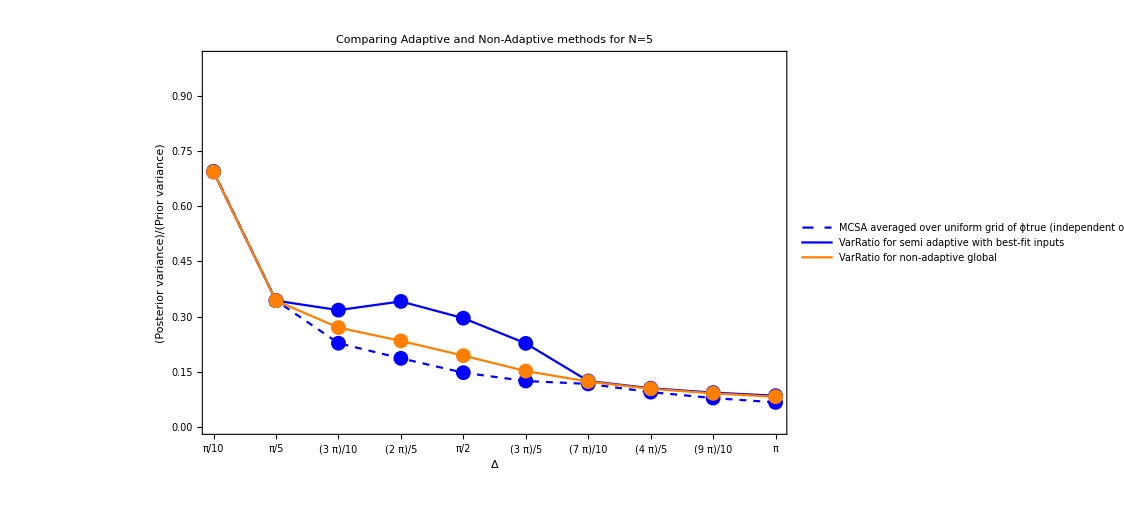

```mathematica
Show[ListPlot[MCSA,PlotStyle->Blue],ListLinePlot[MCSA,PlotStyle->{Blue,Dashed},PlotLegends->{"MCSA averaged over uniform grid of ϕtrue (independent of outcome)"}],ListPlot[VR5,PlotStyle->Blue],ListLinePlot[VR5,PlotStyle->{Blue},PlotLegends->{"VarRatio for semi adaptive with best-fit inputs"}],ListPlot[VRO5,PlotStyle->Orange],ListLinePlot[VRO5,PlotStyle->{Orange},PlotLegends->{"VarRatio for non-adaptive global"}],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Adaptive and Non-Adaptive methods for N=5", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

### Compare Semi-Adaptive Theoretical and Simulation results for 2 shots and Nph=4 (Scalable)

#### MC Semi-Adaptive

```mathematica
MCSAVaryΔ = Table[VarRatioϕtrueGrid=Table[
ntrial=1;
listOfVarRatio=Table[
(*Set the number of photons*)
nph=4;
(*Start with some interval [-Delta,Delta]*)
initInterval =n*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
fVariance=GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=fVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance/(initInterval^2/12),ϕtilde,initInterval}
,{shots,1,nshots}],{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{initInterval, listOfVarRatio[[All,2,1]],phitrue},{phitrue,-initInterval/3,initInterval/3,initInterval/10}];
(*mean VarRatio averaged over uniform grid of ϕtrue*)
Flatten[{initInterval, Mean[VarRatioϕtrueGrid[[All,2]]]}],{n,1,10}];
```

```mathematica
MCSAVaryΔ
```

{{π/10,0.78374},{π/5,0.453609},{(3 π)/10,0.273916},{(2 π)/5,0.235077},{π/2,0.177708},{(3 π)/5,0.143749},{(7 π)/10,0.122459},{(4 π)/5,0.10885},{(9 π)/10,0.104454},{π,0.0886896}}

```mathematica
MCSAVaryΔ={{π/10,0.783739843367726},{π/5,0.45360905567380055},{(3 π)/10,0.2739163064796321},{(2 π)/5,0.2350774296474308},{π/2,0.17770750155811751},{(3 π)/5,0.14374881829066768},{(7 π)/10,0.12245895320127158},{(4 π)/5,0.10885047118339156},{(9 π)/10,0.10445350373540567},{π,0.08868957807323824}}
```

{{π/10,0.78374},{π/5,0.453609},{(3 π)/10,0.273916},{(2 π)/5,0.235077},{π/2,0.177708},{(3 π)/5,0.143749},{(7 π)/10,0.122459},{(4 π)/5,0.10885},{(9 π)/10,0.104454},{π,0.0886896}}

```mathematica
MCSAScalable=MCSAVaryΔ[[All,2]]
```

{0.78374,0.453609,0.273916,0.235077,0.177708,0.143749,0.122459,0.10885,0.104454,0.0886896}

#### Compare plots for SA

```mathematica
(*VarRatio for semi adaptive with best-fit inputs*)
```

```mathematica
VR4
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
VR4={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*VarRatio for non-adaptive global*)
```

```mathematica
VRO4
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

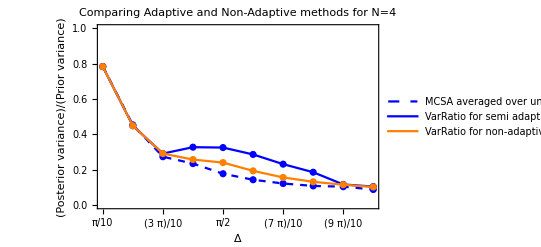

```mathematica
Show[ListPlot[MCSAScalable,PlotStyle->Blue],ListLinePlot[MCSA,PlotStyle->{Blue,Dashed},PlotLegends->{"MCSA averaged over uniform grid of ϕtrue (independent of outcome)"}],ListPlot[VR4,PlotStyle->Blue],ListLinePlot[VR4,PlotStyle->{Blue},PlotLegends->{"VarRatio for semi adaptive with best-fit inputs"}],ListPlot[VRO4,PlotStyle->Orange],ListLinePlot[VRO4,PlotStyle->{Orange},PlotLegends->{"VarRatio for non-adaptive global"}],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Adaptive and Non-Adaptive methods for N=4", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

### Compare Semi-Adaptive Theoretical and Simulation results for 2 shots and Nph=4 (unscalable - plug apt states into global variance)

#### MC Semi-Adaptive

```mathematica
GridOfΔ=Table[(*Set the number of photons*)nph=4;
(*Start with some interval [-Delta,Delta]*)
initInterval =(n *π)/10;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
fVariance=GetVariance[1,nph,delta];
PlugStates=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
variance=fVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
Δinit=Δnext;
Flatten[OptState]
,{shots,1,nshots}];
(*For the first shot*)
Shot1AptStateList = PlugStates[[1]];
(*For the second shot*)
Shot2AptStatetempList = PlugStates[[2]];
(*We want to plug in these individually optimized states into the globally optimized variance to fix assumption about the shape of the uncertainty distribution of 2nd shot being flat*)
Clear[Δ];
Variance24 = GetVariance[2,4,Δ];
(*Change variable names for second shot*)
Shot2AptStateList=Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[n,2]],r[[2,n]]-> Shot2AptStatetempList[[n+nph+1,2]]},{n,1,nph+1}]];
(*Substitution list*)
AptStates = Join[Shot1AptStateList,Shot2AptStateList];
Variance24/.{AptStates}/.Δ->initInterval;
VR4=(Variance24/.{AptStates}/.Δ->initInterval)/(initInterval^2/12);
Flatten[{initInterval,VR4}],{n,1,10}];
```

```mathematica
MCSAVaryΔ=GridOfΔ
```

{{π/10,0.783255},{π/5,0.449095},{(3 π)/10,0.29166},{(2 π)/5,0.327742},{π/2,0.325623},{(3 π)/5,0.286739},{(7 π)/10,0.231896},{(4 π)/5,0.186204},{(9 π)/10,0.117103},{π,0.105124}}

```mathematica
MCSAVaryΔ2={{π/10,0.7832548199807943},{π/5,0.44909545514972116},{(3 π)/10,0.2916602859354953},{(2 π)/5,0.3277416967803197},{π/2,0.32562310100328096},{(3 π)/5,0.28673863672037136},{(7 π)/10,0.23189593990295332},{(4 π)/5,0.18620363615424057},{(9 π)/10,0.11710319710401186},{π,0.10512412877158415}}
```

{{π/10,0.783255},{π/5,0.449095},{(3 π)/10,0.29166},{(2 π)/5,0.327742},{π/2,0.325623},{(3 π)/5,0.286739},{(7 π)/10,0.231896},{(4 π)/5,0.186204},{(9 π)/10,0.117103},{π,0.105124}}

```mathematica
MCSAUnscalable=MCSAVaryΔ2[[All,2]]
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Check with SA Analytic scaling*)
```

#### Compare plots for SA

```mathematica
(*VarRatio for semi adaptive with best-fit inputs. Here we construct the 2 shot variance and plug in states which are apt for single shot *)
```

```mathematica
VR4
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
VR4={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*VarRatio for non-adaptive global*)
```

```mathematica
VRO4
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

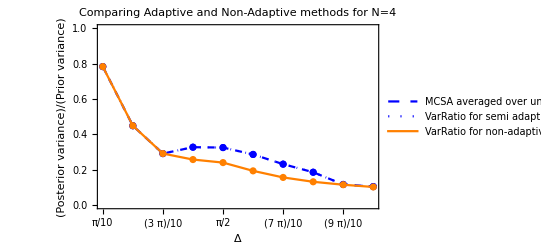

```mathematica
Show[ListPlot[MCSAUnscalable,PlotStyle->Blue],ListLinePlot[MCSAUnscalable,PlotStyle->{Blue,Dashed},PlotLegends->{"MCSA averaged over uniform grid of ϕtrue (independent of outcome)"}],ListPlot[VR4,PlotStyle->{Blue,Dashed}],ListLinePlot[VR4,PlotStyle->{Blue,Dotted},PlotLegends->{"VarRatio for semi adaptive with best-fit inputs"}],ListPlot[VRO4,PlotStyle->Orange],ListLinePlot[VRO4,PlotStyle->{Orange},PlotLegends->{"VarRatio for non-adaptive global"}],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Adaptive and Non-Adaptive methods for N=4", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

### Compare Semi-Adaptive Theoretical and Simulation results for 2 shots and Nph=4 (Scalable and Unscalable together)

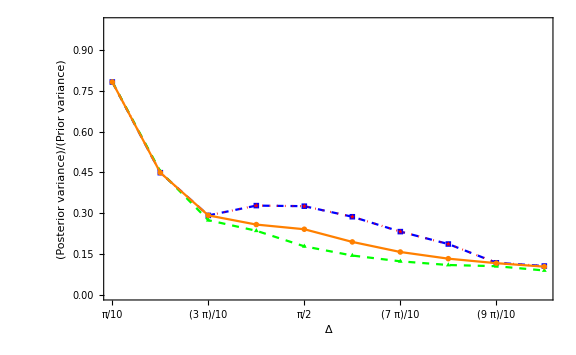

```mathematica
Show[ListLinePlot[MCSAUnscalable,PlotMarkers ->{■,Scaled[0.05]},PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCNA Corrected"},{Right,Top}]],ListLinePlot[MCSAScalable,PlotMarkers ->{▲,Scaled[0.05]},PlotStyle->{Green,Dashed},PlotLegends->Placed[{"MCNA"},{Right,Top}]],ListLinePlot[VR4,PlotMarkers ->{★,Scaled[0.05]},PlotStyle->{Red,Dotted},PlotLegends->Placed[{"Non-adaptive local with best-fit inputs"},{Right,Top}]],ListLinePlot[VRO4,PlotMarkers ->{•,Scaled[0.05]},PlotStyle->{Orange},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},(*PlotLabel-> "Comparing Non-Adaptive methods for N=4",*) PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

## D. Error Analysis MAD ∝ Δposterior

### Semi-adaptive simulation

#### Semi-adaptive simulation

```mathematica
(*Change data with GridOfphi_true*)
```

```mathematica
GridOfϕTrue=Table[
ntrial=1;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=4;
(*Start with some interval [-Delta,Delta]*)
initInterval = π;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = 0.2;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=50;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];

(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
Δnext
,{shots,1,nshots}],{trial,1,ntrial}];
{ϕTrue,listOfPhaseEstimators},{phitrue,0.2,0.2}];
```

```mathematica
GridOfϕTrue
```

{{0.2,{{0.935591,0.0729443}}}}

```mathematica
N[1.3347618125122986^2/12]
```

0.148466

```mathematica
phitilde
```

{1.33476,0.935591,0.622611,0.491695,0.42156,0.375816,0.342789,0.317422,0.297111,0.280352,0.266204,0.254046,0.243446,0.234095,0.225762,0.218274,0.211496,0.205321,0.199665,0.194457,0.189642,0.185171,0.181007,0.177114,0.173464,0.170033,0.1668,0.163747,0.160856,0.158115,0.155511,0.153032,0.150669,0.148413,0.146256,0.144191,0.142212,0.140313,0.138488,0.136733,0.135044,0.133416,0.131846,0.13033,0.128866,0.127451,0.126081,0.124755,0.12347,0.122224}

```mathematica
Table[n,{n,-1.5,1.5,0.3}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

#### Error Analysis for 10 trials of 100 shots

```mathematica
ntrial
```

10

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
GridOfϕTrue
```

{{-1.5,{{0.114922,-1.51009},{0.114922,-1.51542},{0.114922,-1.51385},{0.114922,-1.47526},{0.114922,-1.50492},{0.114922,-1.44873},{0.114922,-1.53745},{0.114922,-1.4452},{0.114922,-1.49622},{0.114922,-1.51596}}},{-1.2,{{0.114922,-1.25484},{0.114922,-1.23835},{0.114922,-1.19757},{0.114922,-1.22201},{0.114922,0.870725},{0.114922,-1.20377},{0.114922,-1.2242},{0.114922,-1.19063},{0.114922,-1.18702},{0.114922,-1.12013}}},{-0.9,{{0.114922,-0.926582},{0.114922,-0.880766},{0.114922,-0.85728},{0.114922,-0.906444},{0.114922,-0.873074},{0.114922,-0.917738},{0.114922,-0.887998},{0.114922,-0.906031},{0.114922,-0.907598},{0.114922,-0.850974}}},{-0.6,{{0.114922,-0.588272},{0.114922,-0.600064},{0.114922,-0.632746},{0.114922,-0.547974},{0.114922,-0.615138},{0.114922,-0.589792},{0.114922,-0.665978},{0.114922,-0.600332},{0.114922,-0.585018},{0.114922,-0.550862}}},{-0.3,{{0.114922,-0.284779},{0.114922,-0.339736},{0.114922,-0.321447},{0.114922,-0.300713},{0.114922,-0.344512},{0.114922,-0.295743},{0.114922,-0.305217},{0.114922,-0.280514},{0.114922,-0.314529},{0.114922,-0.340105}}},{0.,{{0.114922,-2.0929},{0.114922,0.0289112},{0.114922,0.012652},{0.114922,0.0147066},{0.114922,-0.0110046},{0.114922,-0.0103981},{0.114922,0.0121897},{0.114922,-0.0506506},{0.114922,0.054166},{0.114922,-0.0288247}}},{0.3,{{0.114922,0.30831},{0.114922,0.301147},{0.114922,2.20406},{0.114922,0.292064},{0.114922,0.351787},{0.114922,0.295042},{0.114922,0.29032},{0.114922,0.284827},{0.114922,0.316896},{0.114922,0.333141}}},{0.6,{{0.114922,0.523735},{0.114922,0.619163},{0.114922,0.551964},{0.114922,0.61578},{0.114922,0.584708},{0.114922,0.598556},{0.114922,0.601779},{0.114922,0.666727},{0.114922,0.521361},{0.114922,0.565776}}},{0.9,{{0.114922,0.912975},{0.114922,0.833167},{0.114922,0.88246},{0.114922,0.913561},{0.114922,0.94054},{0.114922,0.888192},{0.114922,0.966095},{0.114922,0.936595},{0.114922,0.95887},{0.114922,0.89382}}},{1.2,{{0.114922,1.19544},{0.114922,1.17534},{0.114922,1.23417},{0.114922,1.13563},{0.114922,1.16906},{0.114922,1.24188},{0.114922,1.16373},{0.114922,1.18841},{0.114922,1.20575},{0.114922,1.19273}}},{1.5,{{0.114922,1.53261},{0.114922,1.49355},{0.114922,1.5146},{0.114922,1.52069},{0.114922,1.51643},{0.114922,1.52481},{0.114922,1.52562},{0.114922,1.45571},{0.114922,1.47771},{0.114922,1.49431}}}}

```mathematica
(*Mean of phase estimators over 10 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.49631},{-1.2,-0.99678},{-0.9,-0.891449},{-0.6,-0.597618},{-0.3,-0.31273},{0.,-0.207115},{0.3,0.497759},{0.6,0.584955},{0.9,0.912628},{1.2,1.19021},{1.5,1.5056}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50751},{-1.2,-1.20067},{-0.9,-0.897014},{-0.6,-0.594928},{-0.3,-0.309873},{0.,0.000895805},{0.3,0.304728},{0.6,0.591632},{0.9,0.913268},{1.2,1.19057},{1.5,1.51551}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.000101866},{-1.5,0.000237865},{-1.5,0.000191872},{-1.5,0.000611992},{-1.5,0.0000242366},{-1.5,0.00262855},{-1.5,0.00140257},{-1.5,0.0030034},{-1.5,0.0000142763},{-1.5,0.000254612}},{{-1.2,0.00300752},{-1.2,0.00147076},{-1.2,5.89989×10^-6},{-1.2,0.000484437},{-1.2,4.2879},{-1.2,0.0000141897},{-1.2,0.00058545},{-1.2,0.0000877934},{-1.2,0.000168422},{-1.2,0.00637861}},{{-0.9,0.000706626},{-0.9,0.000369935},{-0.9,0.00182503},{-0.9,0.0000415293},{-0.9,0.000725011},{-0.9,0.00031465},{-0.9,0.000144057},{-0.9,0.0000363721},{-0.9,0.0000577263},{-0.9,0.00240352}},{{-0.6,0.000137543},{-0.6,4.13324×10^-9},{-0.6,0.00107231},{-0.6,0.00270671},{-0.6,0.000229174},{-0.6,0.00010421},{-0.6,0.00435306},{-0.6,1.10271×10^-7},{-0.6,0.000224454},{-0.6,0.00241458}},{{-0.3,0.000231677},{-0.3,0.00157894},{-0.3,0.000459965},{-0.3,5.08396×10^-7},{-0.3,0.00198133},{-0.3,0.0000181211},{-0.3,0.0000272217},{-0.3,0.000379719},{-0.3,0.000211083},{-0.3,0.00160844}},{{0.,4.38021},{0.,0.000835855},{0.,0.000160074},{0.,0.000216285},{0.,0.0001211},{0.,0.00010812},{0.,0.000148588},{0.,0.00256548},{0.,0.00293396},{0.,0.000830865}},{{0.3,0.0000690506},{0.3,1.31508×10^-6},{0.3,3.62544},{0.3,0.0000629782},{0.3,0.00268189},{0.3,0.0000245812},{0.3,0.0000937043},{0.3,0.000230223},{0.3,0.000285468},{0.3,0.00109835}},{{0.6,0.00581642},{0.6,0.000367228},{0.6,0.00230747},{0.6,0.000248995},{0.6,0.000233836},{0.6,2.0864×10^-6},{0.6,3.16441×10^-6},{0.6,0.00445243},{0.6,0.0061841},{0.6,0.0011713}},{{0.9,0.000168338},{0.9,0.00446659},{0.9,0.000307652},{0.9,0.000183898},{0.9,0.00164351},{0.9,0.000139418},{0.9,0.00436858},{0.9,0.00133921},{0.9,0.0034657},{0.9,0.0000381902}},{{1.2,0.0000208033},{1.2,0.000608004},{1.2,0.00116778},{1.2,0.00414368},{1.2,0.000957046},{1.2,0.00175378},{1.2,0.00131542},{1.2,0.000134287},{1.2,0.0000330077},{1.2,0.0000529059}},{{1.5,0.00106357},{1.5,0.0000416271},{1.5,0.000213194},{1.5,0.000427893},{1.5,0.000269799},{1.5,0.000615715},{1.5,0.000656294},{1.5,0.00196119},{1.5,0.000496789},{1.5,0.0000323521}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0100929},{-1.5,0.0154229},{-1.5,0.0138518},{-1.5,0.0247385},{-1.5,0.00492307},{-1.5,0.0512694},{-1.5,0.0374509},{-1.5,0.0548033},{-1.5,0.0037784},{-1.5,0.0159566}},{{-1.2,0.0548408},{-1.2,0.0383505},{-1.2,0.00242897},{-1.2,0.0220099},{-1.2,2.07073},{-1.2,0.00376692},{-1.2,0.0241961},{-1.2,0.00936982},{-1.2,0.0129778},{-1.2,0.0798662}},{{-0.9,0.0265824},{-0.9,0.0192337},{-0.9,0.0427203},{-0.9,0.00644432},{-0.9,0.026926},{-0.9,0.0177384},{-0.9,0.0120024},{-0.9,0.00603093},{-0.9,0.00759778},{-0.9,0.0490257}},{{-0.6,0.0117279},{-0.6,0.0000642903},{-0.6,0.0327461},{-0.6,0.0520261},{-0.6,0.0151385},{-0.6,0.0102083},{-0.6,0.0659777},{-0.6,0.000332071},{-0.6,0.0149818},{-0.6,0.0491384}},{{-0.3,0.015221},{-0.3,0.0397358},{-0.3,0.0214468},{-0.3,0.000713019},{-0.3,0.0445122},{-0.3,0.00425689},{-0.3,0.00521744},{-0.3,0.0194864},{-0.3,0.0145287},{-0.3,0.0401053}},{{0.,2.0929},{0.,0.0289112},{0.,0.012652},{0.,0.0147066},{0.,0.0110046},{0.,0.0103981},{0.,0.0121897},{0.,0.0506506},{0.,0.054166},{0.,0.0288247}},{{0.3,0.00830967},{0.3,0.00114677},{0.3,1.90406},{0.3,0.00793588},{0.3,0.0517869},{0.3,0.00495795},{0.3,0.0096801},{0.3,0.0151731},{0.3,0.0168958},{0.3,0.0331413}},{{0.6,0.0762655},{0.6,0.0191632},{0.6,0.0480361},{0.6,0.0157796},{0.6,0.0152917},{0.6,0.00144444},{0.6,0.00177888},{0.6,0.0667265},{0.6,0.078639},{0.6,0.0342242}},{{0.9,0.0129745},{0.9,0.0668326},{0.9,0.01754},{0.9,0.0135609},{0.9,0.0405403},{0.9,0.0118075},{0.9,0.0660952},{0.9,0.0365952},{0.9,0.0588702},{0.9,0.00617982}},{{1.2,0.00456106},{1.2,0.0246577},{1.2,0.0341727},{1.2,0.0643714},{1.2,0.0309362},{1.2,0.0418782},{1.2,0.0362687},{1.2,0.0115882},{1.2,0.00574523},{1.2,0.00727364}},{{1.5,0.0326125},{1.5,0.00645191},{1.5,0.0146012},{1.5,0.0206856},{1.5,0.0164255},{1.5,0.0248136},{1.5,0.0256182},{1.5,0.0442853},{1.5,0.0222888},{1.5,0.00568789}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

0.000847125

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.49631,0.0291054},{-1.2,-0.99678,0.655752},{-0.9,-0.891449,0.025738},{-0.6,-0.597618,0.0335293},{-0.3,-0.31273,0.0254892},{0.,-0.207115,0.66243},{0.3,0.497759,0.602493},{0.6,0.584955,0.0455928},{0.9,0.912628,0.0401511},{1.2,1.19021,0.0319166},{1.5,1.5056,0.0240384}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50751,0.0156897},{-1.2,-1.20067,0.023103},{-0.9,-0.897014,0.018486},{-0.6,-0.594928,0.0150601},{-0.3,-0.309873,0.0173537},{0.,0.000895805,0.0217657},{0.3,0.304728,0.0124266},{0.6,0.591632,0.0266937},{0.9,0.913268,0.0270676},{1.2,1.19057,0.0277969},{1.5,1.51551,0.0214872}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.4960.029,-1.00.7,-0.8910.026,-0.5980.034,-0.3130.025,-0.20.7,0.50.6,0.580.05,0.910.04,1.1900.032,1.5060.024}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5080.016,-1.2010.023,-0.8970.018,-0.5950.015,-0.3100.017,0.0000.022,0.3050.012,0.5920.027,0.9130.027,1.1910.028,1.5160.021}

```mathematica
(*Mean +- RMSE*)
```

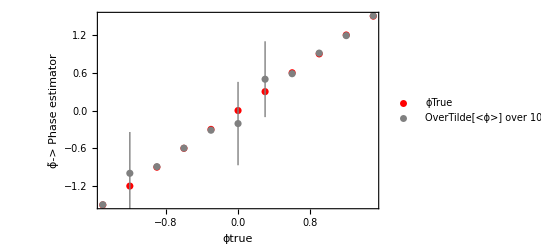

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 10 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*Median +- MAD*)
```

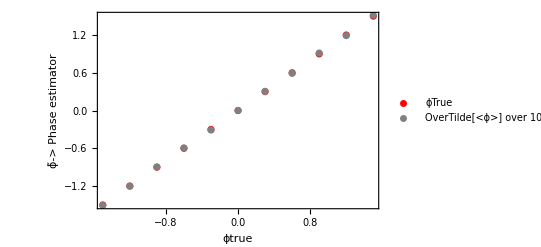

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 10 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*change number of trials and plot error bars*)
```

#### Error Analysis for 30 trials of 100 shots

```mathematica
{ntrial,nshots}
```

{30,100}

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
MatrixForm[GridOfϕTrue]
```

(-1.5 | {{0.114922,-1.51064},{0.114922,-1.53141},{0.114922,-1.5268},{0.114922,-1.50025},{0.114922,-1.48359},{0.114922,-1.47827},{0.114922,-1.46856},{0.114922,-1.53277},{0.114922,-1.45634},{0.114922,-1.47819},{0.114922,-1.52192},{0.114922,-1.46635},{0.114922,-1.51821},{0.114922,-1.48386},{0.114922,-1.52701},{0.114922,-1.50003},{0.114922,-1.52144},{0.114922,-1.45466},{0.114922,-1.50583},{0.114922,-1.4581},{0.114922,-1.5348},{0.114922,-1.46395},{0.114922,-1.49305},{0.114922,-1.50249},{0.114922,-1.4438},{0.114922,-1.27793},{0.114922,-1.52446},{0.114922,-1.5598},{0.114922,-1.50099},{0.114922,-1.49537}}
-1.2 | {{0.114922,-1.19008},{0.114922,-1.21284},{0.114922,-1.21403},{0.114922,-1.2535},{0.114922,-1.23856},{0.114922,-1.19218},{0.114922,-1.21418},{0.114922,-1.17789},{0.114922,-1.26109},{0.114922,-1.2175},{0.114922,-1.25994},{0.114922,-1.20982},{0.114922,-1.2285},{0.114922,-1.22973},{0.114922,-1.2215},{0.114922,-1.22496},{0.114922,-1.20761},{0.114922,-1.20115},{0.114922,-1.20429},{0.114922,-1.19534},{0.114922,-1.19268},{0.114922,-1.20567},{0.114922,-1.25144},{0.114922,-1.22844},{0.114922,-1.22047},{0.114922,-1.19874},{0.114922,-1.19576},{0.114922,-1.21913},{0.114922,-1.18523},{0.114922,0.901628}}
-0.9 | {{0.114922,-0.854594},{0.114922,-0.870026},{0.114922,-0.900624},{0.114922,-0.890917},{0.114922,-0.895027},{0.114922,-0.882016},{0.114922,-0.903404},{0.114922,-0.85628},{0.114922,-0.909089},{0.114922,-0.882838},{0.114922,-0.889179},{0.114922,-0.881457},{0.114922,-0.88767},{0.114922,-0.885518},{0.114922,-0.871208},{0.114922,-0.91162},{0.114922,-0.881448},{0.114922,-0.873328},{0.114922,-0.904436},{0.114922,-0.876281},{0.114922,-0.880626},{0.114922,-0.868105},{0.114922,-0.840229},{0.114922,-0.893054},{0.114922,-0.858646},{0.114922,-0.926111},{0.114922,-0.905636},{0.114922,-0.96301},{0.114922,-0.89177},{0.114922,-0.902156}}
-0.6 | {{0.114922,-0.582327},{0.114922,-0.55193},{0.114922,-0.544272},{0.114922,-0.567414},{0.114922,1.46719},{0.114922,-0.634733},{0.114922,-0.614323},{0.114922,-0.521524},{0.114922,-0.642492},{0.114922,1.50891},{0.114922,-0.572822},{0.114922,-0.589062},{0.114922,-0.595749},{0.114922,-0.587018},{0.114922,-0.626251},{0.114922,-0.602182},{0.114922,-0.555617},{0.114922,-0.549883},{0.114922,-0.583981},{0.114922,-0.524688},{0.114922,-0.576784},{0.114922,-0.663294},{0.114922,-0.566852},{0.114922,-0.568974},{0.114922,1.52649},{0.114922,-0.636562},{0.114922,-0.578778},{0.114922,-0.597864},{0.114922,-0.5892},{0.114922,-0.560859}}
-0.3 | {{0.114922,-0.26178},{0.114922,-0.323937},{0.114922,-0.293749},{0.114922,-0.2867},{0.114922,-0.33688},{0.114922,-0.301407},{0.114922,-0.347111},{0.114922,-0.401526},{0.114922,-0.267591},{0.114922,-0.330249},{0.114922,-0.31636},{0.114922,-0.334912},{0.114922,-0.232476},{0.114922,-0.313922},{0.114922,-0.3053},{0.114922,-0.326337},{0.114922,-0.480967},{0.114922,-0.289377},{0.114922,-0.319038},{0.114922,-2.2857},{0.114922,-0.314829},{0.114922,-0.305724},{0.114922,-0.315518},{0.114922,-0.322557},{0.114922,-0.324471},{0.114922,-0.298171},{0.114922,-0.270795},{0.114922,-0.357263},{0.114922,-0.346408},{0.114922,-0.314967}}
0. | {{0.114922,0.00943495},{0.114922,0.0413921},{0.114922,-0.0151169},{0.114922,-0.00681411},{0.114922,2.11131},{0.114922,0.0103333},{0.114922,-2.09261},{0.114922,0.0245302},{0.114922,-0.0555335},{0.114922,-0.0128722},{0.114922,0.0741048},{0.114922,-0.0168832},{0.114922,-0.0401859},{0.114922,-0.0251832},{0.114922,0.051354},{0.114922,-0.0327132},{0.114922,-2.08779},{0.114922,-0.0415458},{0.114922,-0.0648219},{0.114922,-0.00786404},{0.114922,0.0329538},{0.114922,-0.0506987},{0.114922,0.0243543},{0.114922,-0.00492605},{0.114922,-0.0258355},{0.114922,-0.452114},{0.114922,0.0376497},{0.114922,0.0155196},{0.114922,-0.0232722},{0.114922,0.0320637}}
0.3 | {{0.114922,0.288148},{0.114922,0.295314},{0.114922,0.319267},{0.114922,0.341678},{0.114922,0.264284},{0.114922,0.311046},{0.114922,0.308381},{0.114922,0.304486},{0.114922,0.29006},{0.114922,0.332352},{0.114922,0.297865},{0.114922,0.309447},{0.114922,0.227531},{0.114922,2.36276},{0.114922,0.29244},{0.114922,0.336869},{0.114922,0.296287},{0.114922,0.29349},{0.114922,0.272433},{0.114922,0.300516},{0.114922,0.184497},{0.114922,0.291756},{0.114922,0.267164},{0.114922,0.314724},{0.114922,0.312228},{0.114922,0.264458},{0.114922,2.15629},{0.114922,0.287798},{0.114922,0.378601},{0.114922,0.342565}}
0.6 | {{0.114922,0.67038},{0.114922,0.630133},{0.114922,0.655076},{0.114922,0.585359},{0.114922,0.553036},{0.114922,0.608211},{0.114922,0.632158},{0.114922,0.560166},{0.114922,0.609141},{0.114922,0.621664},{0.114922,0.554383},{0.114922,0.600035},{0.114922,0.509493},{0.114922,0.609424},{0.114922,0.574918},{0.114922,0.638849},{0.114922,0.584491},{0.114922,0.571089},{0.114922,0.610614},{0.114922,0.605236},{0.114922,0.583206},{0.114922,0.606303},{0.114922,0.637179},{0.114922,0.522847},{0.114922,0.541463},{0.114922,0.589237},{0.114922,0.589077},{0.114922,0.635604},{0.114922,0.506999},{0.114922,0.594578}}
0.9 | {{0.114922,0.917212},{0.114922,0.881184},{0.114922,0.900335},{0.114922,0.877224},{0.114922,0.871271},{0.114922,0.848906},{0.114922,0.913182},{0.114922,0.905066},{0.114922,0.884506},{0.114922,0.854518},{0.114922,0.877171},{0.114922,0.972878},{0.114922,0.906656},{0.114922,0.871263},{0.114922,0.916447},{0.114922,0.898322},{0.114922,0.857539},{0.114922,0.851067},{0.114922,0.956809},{0.114922,0.878656},{0.114922,0.919251},{0.114922,0.91421},{0.114922,0.890253},{0.114922,0.935516},{0.114922,0.908804},{0.114922,0.929632},{0.114922,0.860374},{0.114922,0.899124},{0.114922,0.923369},{0.114922,0.864408}}
1.2 | {{0.114922,1.2493},{0.114922,1.17883},{0.114922,1.20094},{0.114922,1.25073},{0.114922,1.25187},{0.114922,1.17407},{0.114922,1.17454},{0.114922,1.26436},{0.114922,1.15838},{0.114922,1.22467},{0.114922,1.20988},{0.114922,1.21169},{0.114922,1.18994},{0.114922,1.1791},{0.114922,1.19523},{0.114922,1.20268},{0.114922,1.24036},{0.114922,1.22664},{0.114922,1.15522},{0.114922,1.16612},{0.114922,1.17807},{0.114922,1.17962},{0.114922,1.18326},{0.114922,1.16341},{0.114922,1.16648},{0.114922,1.22708},{0.114922,1.16232},{0.114922,1.2497},{0.114922,1.23509},{0.114922,1.18665}}
1.5 | {{0.114922,1.50971},{0.114922,1.51339},{0.114922,1.50524},{0.114922,1.4924},{0.114922,1.52729},{0.114922,1.49019},{0.114922,1.49211},{0.114922,1.50806},{0.114922,1.4909},{0.114922,1.46998},{0.114922,1.50752},{0.114922,1.53441},{0.114922,1.46224},{0.114922,1.49948},{0.114922,1.46386},{0.114922,1.50256},{0.114922,1.52227},{0.114922,1.50018},{0.114922,1.4722},{0.114922,1.46543},{0.114922,1.57147},{0.114922,1.50963},{0.114922,1.48435},{0.114922,1.55144},{0.114922,1.46029},{0.114922,1.4555},{0.114922,1.52415},{0.114922,1.49397},{0.114922,1.50972},{0.114922,1.45926}})

```mathematica
(*Mean of phase estimators over 10 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50356},{-1.2,-1.15389},{-0.9,-0.892856},{-0.6,-0.59479},{-0.3,-0.363439},{0.,-0.0384299},{0.3,0.229875},{0.6,0.537372},{0.9,0.910109},{1.2,1.20934},{1.5,1.48801}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50859},{-1.2,-1.19862},{-0.9,-0.890026},{-0.6,-0.594291},{-0.3,-0.293408},{0.,0.0093599},{0.3,0.296},{0.6,0.608169},{0.9,0.914475},{1.2,1.21604},{1.5,1.4925}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.000801124},{-1.5,0.00219302},{-1.5,0.000749748},{-1.5,0.00169184},{-1.5,0.00010795},{-1.5,0.0000906505},{-1.5,0.0000608763},{-1.5,0.000705679},{-1.5,3.27712×10^-6},{-1.5,0.0000878749},{-1.5,0.000608074},{-1.5,0.000246158},{-1.5,0.00020308},{-1.5,0.000362902},{-1.5,0.000990237},{-1.5,3.97475×10^-6},{-1.5,0.00039053},{-1.5,0.00110642},{-1.5,0.000132868},{-1.5,0.00306373},{-1.5,0.00030093},{-1.5,0.000301832},{-1.5,0.0051668},{-1.5,0.0002008},{-1.5,0.0000160221},{-1.5,0.00483491},{-1.5,0.000449641},{-1.5,0.000248095},{-1.5,0.000174274},{-1.5,0.000430449}},{{-1.2,0.0000950585},{-1.2,0.000642656},{-1.2,8.57374×10^-8},{-1.2,0.0019653},{-1.2,0.0009146},{-1.2,0.000161772},{-1.2,7.16807×10^-7},{-1.2,0.00362386},{-1.2,2.07744},{-1.2,0.000955142},{-1.2,0.0015401},{-1.2,3.44933×10^-6},{-1.2,0.000152078},{-1.2,0.00773359},{-1.2,0.0114267},{-1.2,0.000151942},{-1.2,0.000365753},{-1.2,3.64428×10^-6},{-1.2,0.00311632},{-1.2,0.00141556},{-1.2,0.0000315492},{-1.2,0.0000868501},{-1.2,0.00106249},{-1.2,0.0000877223},{-1.2,0.00029394},{-1.2,0.000702286},{-1.2,0.0012427},{-1.2,0.0015822},{-1.2,0.0005966},{-1.2,0.00074481}},{{-0.9,0.00127703},{-0.9,0.00159663},{-0.9,0.00376042},{-0.9,0.00121307},{-0.9,0.0000300258},{-0.9,0.00298625},{-0.9,0.0000428903},{-0.9,0.00392653},{-0.9,0.000328422},{-0.9,0.00231068},{-0.9,0.00109226},{-0.9,0.000976753},{-0.9,0.000438886},{-0.9,0.000974648},{-0.9,0.000149639},{-0.9,0.000179512},{-0.9,0.00245104},{-0.9,0.0011357},{-0.9,0.0000125433},{-0.9,0.000228598},{-0.9,0.00460187},{-0.9,0.00150762},{-0.9,0.0000991491},{-0.9,0.000303016},{-0.9,0.0015198},{-0.9,0.00276463},{-0.9,4.16705×10^-6},{-0.9,0.00396244},{-0.9,0.000436413},{-0.9,0.00197145}},{{-0.6,0.00221581},{-0.6,0.00113953},{-0.6,0.0000329215},{-0.6,0.00398491},{-0.6,0.00190855},{-0.6,0.0000322592},{-0.6,0.00010709},{-0.6,0.0020612},{-0.6,0.000292282},{-0.6,0.0000929557},{-0.6,0.000374006},{-0.6,0.00606987},{-0.6,0.00011479},{-0.6,0.00157471},{-0.6,0.00252868},{-0.6,0.000360824},{-0.6,0.00258443},{-0.6,4.21487×10^-7},{-0.6,0.00377147},{-0.6,9.39848×10^-6},{-0.6,0.00713096},{-0.6,0.00210103},{-0.6,0.00160784},{-0.6,0.000164077},{-0.6,0.000183109},{-0.6,0.00157697},{-0.6,0.00195808},{-0.6,0.000711294},{-0.6,0.000154167},{-0.6,0.000282247}},{{-0.3,0.000336675},{-0.3,0.000203826},{-0.3,0.000021406},{-0.3,0.00356697},{-0.3,0.000804369},{-0.3,0.000817157},{-0.3,3.82875×10^-7},{-0.3,0.0000683067},{-0.3,0.00248986},{-0.3,0.0000467548},{-0.3,0.000171961},{-0.3,0.000231669},{-0.3,0.000300166},{-0.3,0.00907387},{-0.3,0.000768857},{-0.3,0.00223726},{-0.3,0.00045866},{-0.3,0.00055342},{-0.3,0.00524708},{-0.3,0.00011702},{-0.3,0.00134206},{-0.3,0.00449958},{-0.3,0.000119936},{-0.3,0.000283744},{-0.3,0.00162574},{-0.3,2.34026×10^-6},{-0.3,0.0000732433},{-0.3,0.000350091},{-0.3,0.0000293781},{-0.3,4.43581}},{{0.,0.000384385},{0.,0.00244442},{0.,0.000845453},{0.,1.73032},{0.,0.00105237},{0.,0.000205196},{0.,0.0000480618},{0.,0.000316068},{0.,0.000648362},{0.,0.00288193},{0.,0.000559203},{0.,0.0012302},{0.,0.000584953},{0.,0.00143492},{0.,0.00528528},{0.,0.000542855},{0.,0.00282432},{0.,0.000242103},{0.,0.0000311533},{0.,0.000551997},{0.,0.000235414},{0.,0.00044698},{0.,0.0000730533},{0.,0.00105317},{0.,0.000094479},{0.,0.00214293},{0.,0.00404158},{0.,0.0000809957},{0.,0.00047569},{0.,0.0000192926}},{{0.3,0.0015754},{0.3,0.0000645766},{0.3,0.00172499},{0.3,2.01947×10^-6},{0.3,0.00140727},{0.3,0.00192677},{0.3,0.000718972},{0.3,0.000907375},{0.3,0.00687199},{0.3,0.0015541},{0.3,0.0000355789},{0.3,3.16495×10^-7},{0.3,0.000127932},{0.3,0.0000416325},{0.3,0.00359751},{0.3,0.0000276918},{0.3,4.44794},{0.3,0.00374389},{0.3,0.0010365},{0.3,0.00038171},{0.3,0.00184336},{0.3,0.000267954},{0.3,0.000286665},{0.3,0.0000271492},{0.3,0.000456597},{0.3,7.78235×10^-6},{0.3,0.0000734056},{0.3,0.000128173},{0.3,0.00131616},{0.3,0.00188589}},{{0.6,0.000172027},{0.6,0.0000181169},{0.6,0.00173151},{0.6,0.00318655},{0.6,0.00151965},{0.6,0.000476975},{0.6,0.0000334837},{0.6,0.00207463},{0.6,0.000422134},{0.6,0.00723402},{0.6,0.000388033},{0.6,0.000247394},{0.6,0.0000797503},{0.6,3.12648×10^-6},{0.6,3.59742×10^-7},{0.6,0.000717679},{0.6,0.00533953},{0.6,0.00318368},{0.6,0.000822488},{0.6,0.00300373},{0.6,0.0000671295},{0.6,0.0011298},{0.6,0.000728755},{0.6,0.000111344},{0.6,0.000250532},{0.6,0.000125917},{0.6,0.00220268},{0.6,0.00106151},{0.6,4.45835},{0.6,0.00124442}},{{0.9,0.00111862},{0.9,0.000665428},{0.9,7.2784×10^-7},{0.9,0.000651329},{0.9,0.000494212},{0.9,0.000137892},{0.9,0.000147495},{0.9,0.000241272},{0.9,0.000924075},{0.9,0.00187708},{0.9,0.000484945},{0.9,0.000256626},{0.9,0.00154766},{0.9,0.0000109621},{0.9,0.00366703},{0.9,0.00435075},{0.9,0.0000644246},{0.9,0.000819192},{0.9,0.000239942},{0.9,2.38989×10^-6},{0.9,0.000942252},{0.9,0.000753578},{0.9,0.000433977},{0.9,0.000504025},{0.9,0.00241829},{0.9,4.89506×10^-11},{0.9,0.000181191},{0.9,0.0044013},{0.9,0.000114311},{0.9,0.000837544}},{{1.2,0.000311315},{1.2,0.00134147},{1.2,0.000485083},{1.2,4.0316×10^-6},{1.2,0.000166621},{1.2,0.00986613},{1.2,0.00145012},{1.2,0.000571893},{1.2,0.000300706},{1.2,6.45929×10^-6},{1.2,0.000508936},{1.2,0.000216957},{1.2,0.00156046},{1.2,0.000491368},{1.2,2.06886×10^-6},{1.2,0.00176666},{1.2,0.000947295},{1.2,0.00141112},{1.2,0.0015715},{1.2,0.00548787},{1.2,0.000225554},{1.2,0.0000214211},{1.2,0.0000965721},{1.2,0.000652996},{1.2,0.00177248},{1.2,0.000444412},{1.2,0.000313397},{1.2,0.00215264},{1.2,0.00288896},{1.2,0.00238902}},{{1.5,0.000291186},{1.5,0.000648772},{1.5,0.000215398},{1.5,0.0000120985},{1.5,0.0011532},{1.5,0.00937393},{1.5,0.00668217},{1.5,1.33855×10^-6},{1.5,0.0000302364},{1.5,0.0000415268},{1.5,0.00190352},{1.5,0.00134347},{1.5,0.00317806},{1.5,0.0000147729},{1.5,0.00183223},{1.5,0.000588152},{1.5,5.23357×10^-7},{1.5,0.0000191869},{1.5,0.0000901125},{1.5,6.73279×10^-6},{1.5,0.0068917},{1.5,9.55665×10^-7},{1.5,0.000105495},{1.5,0.000750319},{1.5,0.00118424},{1.5,0.000015},{1.5,0.00123644},{1.5,0.000461263},{1.5,0.00069946},{1.5,0.000344423}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0283041},{-1.5,0.0468297},{-1.5,0.0273815},{-1.5,0.041132},{-1.5,0.0103899},{-1.5,0.00952106},{-1.5,0.00780233},{-1.5,0.0265646},{-1.5,0.00181028},{-1.5,0.00937416},{-1.5,0.0246592},{-1.5,0.0156894},{-1.5,0.0142506},{-1.5,0.01905},{-1.5,0.031468},{-1.5,0.00199368},{-1.5,0.0197618},{-1.5,0.0332629},{-1.5,0.0115268},{-1.5,0.055351},{-1.5,0.0173473},{-1.5,0.0173733},{-1.5,0.0718805},{-1.5,0.0141704},{-1.5,0.00400276},{-1.5,0.0695335},{-1.5,0.0212047},{-1.5,0.015751},{-1.5,0.0132013},{-1.5,0.0207473}},{{-1.2,0.00974979},{-1.2,0.0253507},{-1.2,0.000292809},{-1.2,0.0443317},{-1.2,0.0302424},{-1.2,0.012719},{-1.2,0.000846644},{-1.2,0.0601985},{-1.2,1.44133},{-1.2,0.0309054},{-1.2,0.0392442},{-1.2,0.00185724},{-1.2,0.012332},{-1.2,0.0879408},{-1.2,0.106896},{-1.2,0.0123265},{-1.2,0.0191247},{-1.2,0.001909},{-1.2,0.055824},{-1.2,0.0376239},{-1.2,0.00561687},{-1.2,0.00931934},{-1.2,0.0325959},{-1.2,0.00936602},{-1.2,0.0171447},{-1.2,0.0265007},{-1.2,0.035252},{-1.2,0.0397769},{-1.2,0.0244254},{-1.2,0.0272912}},{{-0.9,0.0357356},{-0.9,0.0399578},{-0.9,0.0613223},{-0.9,0.0348291},{-0.9,0.00547958},{-0.9,0.0546466},{-0.9,0.00654907},{-0.9,0.062662},{-0.9,0.0181224},{-0.9,0.0480696},{-0.9,0.0330493},{-0.9,0.031253},{-0.9,0.0209496},{-0.9,0.0312193},{-0.9,0.0122327},{-0.9,0.0133982},{-0.9,0.049508},{-0.9,0.0337002},{-0.9,0.00354165},{-0.9,0.0151195},{-0.9,0.0678371},{-0.9,0.0388281},{-0.9,0.00995736},{-0.9,0.0174073},{-0.9,0.0389846},{-0.9,0.0525798},{-0.9,0.00204134},{-0.9,0.0629479},{-0.9,0.0208905},{-0.9,0.044401}},{{-0.6,0.0470724},{-0.6,0.0337569},{-0.6,0.00573773},{-0.6,0.0631262},{-0.6,0.0436869},{-0.6,0.00567972},{-0.6,0.0103484},{-0.6,0.0454004},{-0.6,0.0170962},{-0.6,0.00964135},{-0.6,0.0193392},{-0.6,0.0779094},{-0.6,0.010714},{-0.6,0.0396826},{-0.6,0.050286},{-0.6,0.0189954},{-0.6,0.0508373},{-0.6,0.000649221},{-0.6,0.0614123},{-0.6,0.00306569},{-0.6,0.084445},{-0.6,0.045837},{-0.6,0.0400978},{-0.6,0.0128093},{-0.6,0.0135318},{-0.6,0.0397111},{-0.6,0.0442502},{-0.6,0.0266701},{-0.6,0.0124164},{-0.6,0.0168002}},{{-0.3,0.0183487},{-0.3,0.0142768},{-0.3,0.00462666},{-0.3,0.0597241},{-0.3,0.0283614},{-0.3,0.028586},{-0.3,0.000618769},{-0.3,0.00826479},{-0.3,0.0498985},{-0.3,0.00683775},{-0.3,0.0131134},{-0.3,0.0152207},{-0.3,0.0173253},{-0.3,0.0952569},{-0.3,0.0277283},{-0.3,0.0472997},{-0.3,0.0214163},{-0.3,0.0235249},{-0.3,0.0724367},{-0.3,0.0108176},{-0.3,0.0366341},{-0.3,0.0670789},{-0.3,0.0109515},{-0.3,0.0168447},{-0.3,0.0403205},{-0.3,0.00152979},{-0.3,0.00855823},{-0.3,0.0187107},{-0.3,0.00542015},{-0.3,2.10614}},{{0.,0.0196057},{0.,0.0494411},{0.,0.0290767},{0.,1.31542},{0.,0.0324402},{0.,0.0143247},{0.,0.00693266},{0.,0.0177783},{0.,0.025463},{0.,0.0536836},{0.,0.0236475},{0.,0.0350743},{0.,0.0241858},{0.,0.0378803},{0.,0.0727},{0.,0.0232992},{0.,0.0531443},{0.,0.0155597},{0.,0.00558152},{0.,0.0234946},{0.,0.0153432},{0.,0.0211419},{0.,0.00854713},{0.,0.0324525},{0.,0.00972003},{0.,0.0462917},{0.,0.0635734},{0.,0.00899976},{0.,0.0218103},{0.,0.00439233}},{{0.3,0.0396914},{0.3,0.00803596},{0.3,0.041533},{0.3,0.00142108},{0.3,0.0375137},{0.3,0.043895},{0.3,0.0268137},{0.3,0.0301227},{0.3,0.0828975},{0.3,0.0394221},{0.3,0.00596481},{0.3,0.000562579},{0.3,0.0113107},{0.3,0.00645233},{0.3,0.0599793},{0.3,0.0052623},{0.3,2.10901},{0.3,0.0611874},{0.3,0.0321946},{0.3,0.0195374},{0.3,0.0429344},{0.3,0.0163693},{0.3,0.0169312},{0.3,0.00521049},{0.3,0.0213681},{0.3,0.00278969},{0.3,0.00856771},{0.3,0.0113214},{0.3,0.036279},{0.3,0.0434268}},{{0.6,0.0131159},{0.6,0.0042564},{0.6,0.0416114},{0.6,0.0564496},{0.6,0.0389827},{0.6,0.0218398},{0.6,0.00578651},{0.6,0.0455481},{0.6,0.0205459},{0.6,0.085053},{0.6,0.0196986},{0.6,0.0157288},{0.6,0.0089303},{0.6,0.00176819},{0.6,0.000599785},{0.6,0.0267895},{0.6,0.0730721},{0.6,0.0564241},{0.6,0.0286791},{0.6,0.0548063},{0.6,0.00819326},{0.6,0.0336125},{0.6,0.0269955},{0.6,0.010552},{0.6,0.0158282},{0.6,0.0112213},{0.6,0.0469327},{0.6,0.0325809},{0.6,2.11148},{0.6,0.0352763}},{{0.9,0.0334457},{0.9,0.0257959},{0.9,0.000853136},{0.9,0.0255211},{0.9,0.0222309},{0.9,0.0117427},{0.9,0.0121448},{0.9,0.0155329},{0.9,0.0303986},{0.9,0.0433252},{0.9,0.0220215},{0.9,0.0160196},{0.9,0.0393404},{0.9,0.00331091},{0.9,0.060556},{0.9,0.0659602},{0.9,0.0080265},{0.9,0.0286215},{0.9,0.0154901},{0.9,0.00154593},{0.9,0.0306961},{0.9,0.0274514},{0.9,0.0208321},{0.9,0.0224505},{0.9,0.0491761},{0.9,6.99647×10^-6},{0.9,0.0134607},{0.9,0.0663423},{0.9,0.0106916},{0.9,0.0289404}},{{1.2,0.0176441},{1.2,0.0366261},{1.2,0.0220246},{1.2,0.00200789},{1.2,0.0129082},{1.2,0.0993284},{1.2,0.0380804},{1.2,0.0239143},{1.2,0.0173409},{1.2,0.00254151},{1.2,0.0225596},{1.2,0.0147295},{1.2,0.0395026},{1.2,0.0221668},{1.2,0.00143835},{1.2,0.0420317},{1.2,0.0307782},{1.2,0.0375649},{1.2,0.0396422},{1.2,0.0740801},{1.2,0.0150185},{1.2,0.00462829},{1.2,0.00982711},{1.2,0.0255538},{1.2,0.0421008},{1.2,0.0210811},{1.2,0.017703},{1.2,0.0463966},{1.2,0.0537491},{1.2,0.0488776}},{{1.5,0.0170642},{1.5,0.025471},{1.5,0.0146764},{1.5,0.00347829},{1.5,0.0339588},{1.5,0.096819},{1.5,0.0817446},{1.5,0.00115696},{1.5,0.00549877},{1.5,0.00644413},{1.5,0.0436294},{1.5,0.0366534},{1.5,0.0563743},{1.5,0.00384355},{1.5,0.0428046},{1.5,0.0242519},{1.5,0.000723434},{1.5,0.00438029},{1.5,0.00949276},{1.5,0.00259476},{1.5,0.0830163},{1.5,0.000977581},{1.5,0.0102711},{1.5,0.027392},{1.5,0.0344129},{1.5,0.00387299},{1.5,0.0351631},{1.5,0.021477},{1.5,0.0264473},{1.5,0.0185586}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

0.13822

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50356,0.0292824},{-1.2,-1.15389,0.265715},{-0.9,-0.892856,0.037542},{-0.6,-0.59479,0.038784},{-0.3,-0.363439,0.386076},{0.,-0.0384299,0.242288},{0.3,0.229875,0.386436},{0.6,0.537372,0.387123},{0.9,0.910109,0.0307075},{1.2,1.20934,0.0362517},{1.5,1.48801,0.0361091}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50859,0.0182116},{-1.2,-1.19862,0.0259257},{-0.9,-0.890026,0.0333748},{-0.6,-0.594291,0.0302135},{-0.3,-0.293408,0.0185297},{0.,0.0093599,0.023571},{0.3,0.296,0.0240909},{0.6,0.608169,0.0268925},{0.9,0.914475,0.0223407},{1.2,1.21604,0.0232369},{1.5,1.4925,0.0200178}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotResults={-1.5,-1.2,-0.9,-0.6000000000000001,-0.30000000000000004,0.,0.2999999999999998,0.6000000000000001,0.8999999999999999,1.1999999999999997,1.5}
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotMAD=Table[Resultsmad[[m,3]],{m,1,Length[GridOfϕTrue]}]
```

{0.0182116,0.0259257,0.0333748,0.0302135,0.0185297,0.023571,0.0240909,0.0268925,0.0223407,0.0232369,0.0200178}

```mathematica
PlotMAD={0.018211649735912938,0.025925671606073175,0.03337477817408602,0.030213513349429844,0.01852970684742128,0.023571043927632054,0.024090887272511186,0.026892495961010288,0.022340687350730137,0.023236948244747646,0.020017836731376137}
```

{0.0182116,0.0259257,0.0333748,0.0302135,0.0185297,0.023571,0.0240909,0.0268925,0.0223407,0.0232369,0.0200178}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5040.029,-1.150.27,-0.890.04,-0.590.04,-0.40.4,-0.040.24,0.20.4,0.50.4,0.9100.031,1.210.04,1.490.04}

```mathematica
PlotDevRMSE={-1.5040.029,-1.150.27,-0.890.04,-0.590.04,-0.40.4,-0.040.24,0.20.4,0.50.4,0.9100.031,1.210.04,1.490.04}
```

{-1.5040.029,-1.150.27,-0.890.04,-0.590.04,-0.40.4,-0.040.24,0.20.4,0.50.4,0.9100.031,1.210.04,1.490.04}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5090.018,-1.1990.026,-0.8900.033,-0.5940.030,-0.2930.019,0.0090.024,0.2960.024,0.6080.027,0.9140.022,1.2160.023,1.4930.020}

```mathematica
PlotDevMAD={-1.5090.018,-1.1990.026,-0.8900.033,-0.5940.030,-0.2930.019,0.0090.024,0.2960.024,0.6080.027,0.9140.022,1.2160.023,1.4930.020}
```

{-1.5090.018,-1.1990.026,-0.8900.033,-0.5940.030,-0.2930.019,0.0090.024,0.2960.024,0.6080.027,0.9140.022,1.2160.023,1.4930.020}

```mathematica
(*Mean +- RMSE*)
```

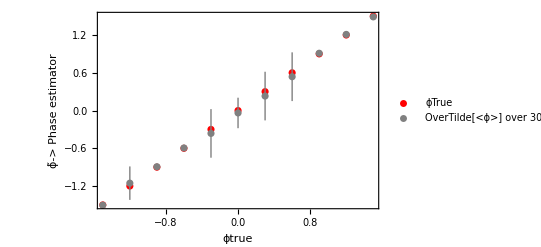

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 30 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*Median +- MAD*)
```

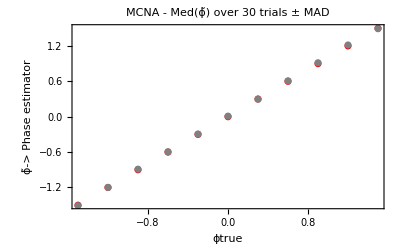

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->Placed[{"ϕTrue"},{Right,Center}]],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->Placed[{"Med(ϕ̃) ± MAD"},{Right,Center}]], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}, PlotLabel->"MCNA - Med(ϕ̃) over 30 trials ± MAD"]
```

```mathematica
(*MAD vs Δ*)
```

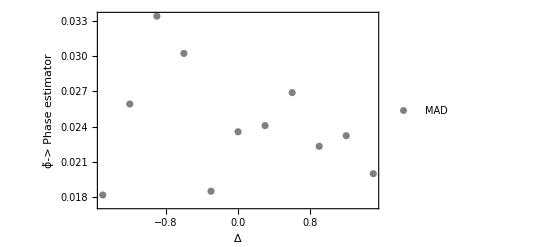

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotMAD}],PlotStyle->{Gray}, PlotLegends->{"MAD"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"Δ",Style["ϕ̃-> Phase estimator",Thick]}]
```

### Nph = 3

#### MAD ∝ Δposterior

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,3,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}];Resultsmad=Table[{GridOfϕTrue[[del,3,1,1]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]];
{del*π/10,Resultsmad},{del,{1,2,3,4,5,10}}];
```

```mathematica
GridOfϕTrue;
```

```mathematica
Data;
```

```mathematica
(*Plotting the average of the median absolute deviation (over different values of ϕtrue) against the posterior uncertainty Δ*)
```

```mathematica
MADΔPlot=Table[{Data[[del,2,1,1]],Mean[Data[[del,2,All,2]]]},{del,1,Length[Data]}]
```

{{0.237017,0.054258},{0.309312,0.0641202},{0.3295,0.0682761},{0.338989,0.0677325},{0.348644,0.0740478},{0.364522,0.0800851}}

```mathematica
(*Best-fit line*)
```

```mathematica
bfline = Fit[MADΔPlot,{1,x},x]
```

0.00879904+0.184506 x

```mathematica
bfline2=0.67449/√12 x
```

0.194708 x

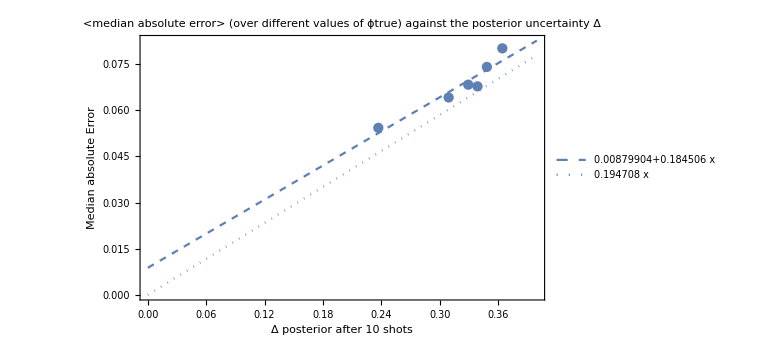

```mathematica
Show[Plot[bfline,{x,0,0.4},PlotLegends->{bfline}, PlotStyle->Dashed],Plot[bfline2,{x,0,0.4},PlotLegends->{bfline2}, PlotStyle->Dotted],ListPlot[MADΔPlot,Frame->True,FrameTicks->Automatic],Frame-> True,FrameTicks->Automatic,FrameLabel->{"Δ posterior after 10 shots",Style["Median absolute Error",Thick]},PlotRange->All,ImageSize->Large, AxesOrigin->{0,0},PlotLabel-> "<median absolute error> (over different values of ϕtrue) against the posterior uncertainty Δ"]
```

```mathematica
(*Assuming normally distributed error terms, MAD = σ √2 erf^-1(1/2) ≃ 0.67449 σ, where σ=std.dev. \ref Wikipedia*)
```

```mathematica
(*σ=Δ/(2 √3)*)
```

```mathematica
N[InverseErf[1/2]*√2]
```

0.67449

```mathematica
(*MAD = Δ/(2 √3)0.67449=(Δ0.67449)/(√12)*)
```

```mathematica
N[0.67449/√12]
```

0.194708

```mathematica
(*MAD ∝ RMS*)
```

#### MAD ∝ Δposterior check smaller uncertainties

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/50;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-initInterval/2,initInterval/2,initInterval/10}];
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,3,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}];Resultsmad=Table[{GridOfϕTrue[[del,3,1,1]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]];
{del*π/10,Resultsmad},{del,{1,2,3,4,5,10}}];
```

```mathematica
GridOfϕTrue;
```

```mathematica
Data;
```

```mathematica
(*Plotting the average of the median absolute deviation (over different values of ϕtrue) against the posterior uncertainty Δ*)
```

```mathematica
MADΔPlot=Table[{Data[[del,2,1,1]],Mean[Data[[del,2,All,2]]]},{del,1,Length[Data]}]
```

{{0.0619208,0.0167873},{0.118796,0.016828},{0.167327,0.0293902},{0.206508,0.0398459},{0.237017,0.0464312},{0.309312,0.0560246}}

```mathematica
(*Best-fit line*)
```

```mathematica
bfline = Fit[MADΔPlot,{1,x},x]
```

0.00153591+0.178123 x

```mathematica
bfline2=0.67449/√12 x
```

0.194708 x

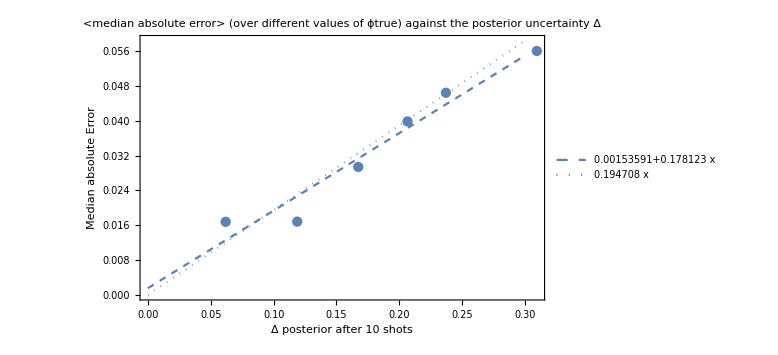

```mathematica
Show[Plot[bfline,{x,0,0.3},PlotLegends->{bfline}, PlotStyle->Dashed],Plot[bfline2,{x,0,0.3},PlotLegends->{bfline2}, PlotStyle->Dotted],ListPlot[MADΔPlot,Frame->True,FrameTicks->Automatic],Frame-> True,FrameTicks->Automatic,FrameLabel->{"Δ posterior after 10 shots",Style["Median absolute Error",Thick]},PlotRange->All,ImageSize->Large, AxesOrigin->{0,0},PlotLabel-> "<median absolute error> (over different values of ϕtrue) against the posterior uncertainty Δ"]
```

```mathematica
(*Assuming normally distributed error terms, MAD = σ √2 erf^-1(1/2) ≃ 0.67449 σ, where σ=std.dev. \ref Wikipedia*)
```

```mathematica
(*σ=Δ/(2 √3)*)
```

```mathematica
N[InverseErf[1/2]*√2]
```

0.67449

```mathematica
(*MAD = Δ/(2 √3)0.67449=(Δ0.67449)/(√12)*)
```

```mathematica
N[0.67449/√12]
```

0.194708

```mathematica
(*MAD ∝ RMS*)
```

#### MAD ∝ Δposterior check even smaller uncertainties

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/100;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-initInterval/2,initInterval/2,initInterval/10}];
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,3,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}];Resultsmad=Table[{GridOfϕTrue[[del,3,1,1]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]];
{del*π/10,Resultsmad},{del,{1,2,3,4,5,10}}];
```

```mathematica
GridOfϕTrue;
```

```mathematica
Data;
```

```mathematica
(*Plotting the average of the median absolute deviation (over different values of ϕtrue) against the posterior uncertainty Δ*)
```

```mathematica
MADΔPlot=Table[{Data[[del,2,1,1]],Mean[Data[[del,2,All,2]]]},{del,1,Length[Data]}]
```

{{0.0313003,0.00856796},{0.0619208,0.00874},{0.0912497,0.0168974},{0.118796,0.0243047},{0.144218,0.0297436},{0.237017,0.0373242}}

```mathematica
(*Best-fit line*)
```

```mathematica
bfline = Fit[MADΔPlot,{1,x},x]
```

0.0032608+0.154876 x

```mathematica
bfline2=0.67449/√12 x
```

0.194708 x

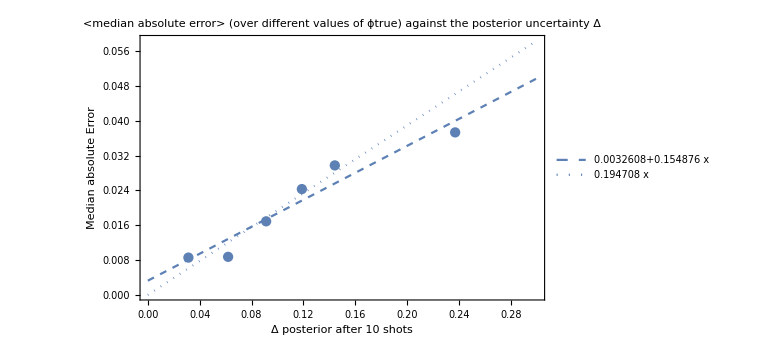

```mathematica
Show[Plot[bfline,{x,0,0.3},PlotLegends->{bfline}, PlotStyle->Dashed],Plot[bfline2,{x,0,0.3},PlotLegends->{bfline2}, PlotStyle->Dotted],ListPlot[MADΔPlot,Frame->True,FrameTicks->Automatic],Frame-> True,FrameTicks->Automatic,FrameLabel->{"Δ posterior after 10 shots",Style["Median absolute Error",Thick]},PlotRange->All,ImageSize->Large, AxesOrigin->{0,0},PlotLabel-> "<median absolute error> (over different values of ϕtrue) against the posterior uncertainty Δ"]
```

```mathematica
(*Assuming normally distributed error terms, MAD = σ √2 erf^-1(1/2) ≃ 0.67449 σ, where σ=std.dev. \ref Wikipedia*)
```

```mathematica
(*σ=Δ/(2 √3)*)
```

```mathematica
N[InverseErf[1/2]*√2]
```

0.67449

```mathematica
(*MAD = Δ/(2 √3)0.67449=(Δ0.67449)/(√12)*)
```

```mathematica
N[0.67449/√12]
```

0.194708

```mathematica
(*MAD ∝ RMS*)
```

#### Combined plot

```mathematica
MADΔPlot={{0.03130026061978462,0.008567963376654783},{0.06192078398016521,0.008740002871793566},{0.09124965487499723,0.016897393066648017},{0.1187958025256504,0.024304688766211138},{0.1442178660444397,0.029743617026781587},{0.23701694674932283,0.03732423772003454},{0.06192078398016521,0.0167872647317295},{0.1187958025256504,0.01682802031740487},{0.16732749743122943,0.02939015566157268},{0.20650772888752153,0.039845881979367975},{0.23701694674932283,0.04643121380650978},{0.3093120277754238,0.05602457618513643},{0.23701694674932283,0.05425797250663709},{0.3093120277754238,0.06412022629788798},{0.329499633081844,0.06827605349325895},{0.3389894050765066,0.067732538696121},{0.34864437396234893,0.07404781900365966},{0.3645222931057801,0.08008511513919117}};
```

```mathematica
(*Best-fit line*)
bfline = Fit[MADΔPlot,{1,Δ},Δ]
```

-0.0020041+0.208834 Δ

```mathematica
bfline2=0.67449/√12 Δ
```

0.194708 Δ

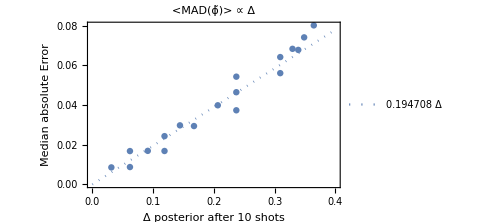

```mathematica
Show[Plot[bfline2,{Δ,0,0.4},PlotLegends->Placed[{bfline2},{Right,Center}], PlotStyle->Dotted],ListPlot[MADΔPlot,Frame->True,FrameTicks->Automatic],Frame-> True,FrameTicks->Automatic,FrameLabel->{"Δ posterior after 10 shots",Style["Median absolute Error",Thick]},PlotRange->All,ImageSize->Medium, AxesOrigin->{0,0},PlotLabel-> "<MAD(ϕ̃)> ∝ Δ"]
```

## E. Probability of being unlucky - Monte Carlo check

### Nph = 3

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
ntrial=100
```

100

```mathematica
Data
```

{(-π/20 | -1 | 0.67 | π/10
-π/25 | -4/5 | 0.88 | π/10
-(3 π)/100 | -3/5 | 0.94 | π/10
-π/50 | -2/5 | 0.98 | π/10
-π/100 | -1/5 | 0.99 | π/10
0 | 0 | 0.99 | π/10
π/100 | 1/5 | 0.98 | π/10
π/50 | 2/5 | 0.95 | π/10
(3 π)/100 | 3/5 | 0.91 | π/10
π/25 | 4/5 | 0.82 | π/10
π/20 | 1 | 0.75 | π/10),(-π/10 | -1 | 0.86 | π/5
-(2 π)/25 | -4/5 | 0.89 | π/5
-(3 π)/50 | -3/5 | 0.94 | π/5
-π/25 | -2/5 | 0.95 | π/5
-π/50 | -1/5 | 0.94 | π/5
0 | 0 | 0.94 | π/5
π/50 | 1/5 | 0.96 | π/5
π/25 | 2/5 | 0.94 | π/5
(3 π)/50 | 3/5 | 0.96 | π/5
(2 π)/25 | 4/5 | 0.91 | π/5
π/10 | 1 | 0.87 | π/5),(-(3 π)/20 | -1 | 0.9 | (3 π)/10
-(3 π)/25 | -4/5 | 0.91 | (3 π)/10
-(9 π)/100 | -3/5 | 0.92 | (3 π)/10
-(3 π)/50 | -2/5 | 0.91 | (3 π)/10
-(3 π)/100 | -1/5 | 0.88 | (3 π)/10
0 | 0 | 0.92 | (3 π)/10
(3 π)/100 | 1/5 | 0.91 | (3 π)/10
(3 π)/50 | 2/5 | 0.93 | (3 π)/10
(9 π)/100 | 3/5 | 0.97 | (3 π)/10
(3 π)/25 | 4/5 | 0.92 | (3 π)/10
(3 π)/20 | 1 | 0.89 | (3 π)/10),(-π/5 | -1 | 0.89 | (2 π)/5
-(4 π)/25 | -4/5 | 0.91 | (2 π)/5
-(3 π)/25 | -3/5 | 0.91 | (2 π)/5
-(2 π)/25 | -2/5 | 0.93 | (2 π)/5
-π/25 | -1/5 | 0.91 | (2 π)/5
0 | 0 | 0.9 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.95 | (2 π)/5
(3 π)/25 | 3/5 | 0.91 | (2 π)/5
(4 π)/25 | 4/5 | 0.9 | (2 π)/5
π/5 | 1 | 0.91 | (2 π)/5),(-π/4 | -1 | 0.78 | π/2
-π/5 | -4/5 | 0.89 | π/2
-(3 π)/20 | -3/5 | 0.89 | π/2
-π/10 | -2/5 | 0.84 | π/2
-π/20 | -1/5 | 0.9 | π/2
0 | 0 | 0.88 | π/2
π/20 | 1/5 | 0.95 | π/2
π/10 | 2/5 | 0.92 | π/2
(3 π)/20 | 3/5 | 0.91 | π/2
π/5 | 4/5 | 0.87 | π/2
π/4 | 1 | 0.79 | π/2),(-π/2 | -1 | 0.94 | π
-(2 π)/5 | -4/5 | 0.87 | π
-(3 π)/10 | -3/5 | 0.91 | π
-π/5 | -2/5 | 0.86 | π
-π/10 | -1/5 | 0.84 | π
0 | 0 | 0.84 | π
π/10 | 1/5 | 0.87 | π
π/5 | 2/5 | 0.86 | π
(3 π)/10 | 3/5 | 0.91 | π
(2 π)/5 | 4/5 | 0.89 | π
π/2 | 1 | 0.9 | π)}

```mathematica
Data={({{-π/20, -1, 0.67, π/10}, {-π/25, -4/5, 0.88, π/10}, {-(3 π)/100, -3/5, 0.94, π/10}, {-π/50, -2/5, 0.98, π/10}, {-π/100, -1/5, 0.99, π/10}, {0, 0, 0.99, π/10}, {π/100, 1/5, 0.98, π/10}, {π/50, 2/5, 0.95, π/10}, {(3 π)/100, 3/5, 0.91, π/10}, {π/25, 4/5, 0.82, π/10}, {π/20, 1, 0.75, π/10}}),({{-π/10, -1, 0.86, π/5}, {-(2 π)/25, -4/5, 0.89, π/5}, {-(3 π)/50, -3/5, 0.94, π/5}, {-π/25, -2/5, 0.95, π/5}, {-π/50, -1/5, 0.94, π/5}, {0, 0, 0.94, π/5}, {π/50, 1/5, 0.96, π/5}, {π/25, 2/5, 0.94, π/5}, {(3 π)/50, 3/5, 0.96, π/5}, {(2 π)/25, 4/5, 0.91, π/5}, {π/10, 1, 0.87, π/5}}),({{-(3 π)/20, -1, 0.9, (3 π)/10}, {-(3 π)/25, -4/5, 0.91, (3 π)/10}, {-(9 π)/100, -3/5, 0.92, (3 π)/10}, {-(3 π)/50, -2/5, 0.91, (3 π)/10}, {-(3 π)/100, -1/5, 0.88, (3 π)/10}, {0, 0, 0.92, (3 π)/10}, {(3 π)/100, 1/5, 0.91, (3 π)/10}, {(3 π)/50, 2/5, 0.93, (3 π)/10}, {(9 π)/100, 3/5, 0.97, (3 π)/10}, {(3 π)/25, 4/5, 0.92, (3 π)/10}, {(3 π)/20, 1, 0.89, (3 π)/10}}),({{-π/5, -1, 0.89, (2 π)/5}, {-(4 π)/25, -4/5, 0.91, (2 π)/5}, {-(3 π)/25, -3/5, 0.91, (2 π)/5}, {-(2 π)/25, -2/5, 0.93, (2 π)/5}, {-π/25, -1/5, 0.91, (2 π)/5}, {0, 0, 0.9, (2 π)/5}, {π/25, 1/5, 0.91, (2 π)/5}, {(2 π)/25, 2/5, 0.95, (2 π)/5}, {(3 π)/25, 3/5, 0.91, (2 π)/5}, {(4 π)/25, 4/5, 0.9, (2 π)/5}, {π/5, 1, 0.91, (2 π)/5}}),({{-π/4, -1, 0.78, π/2}, {-π/5, -4/5, 0.89, π/2}, {-(3 π)/20, -3/5, 0.89, π/2}, {-π/10, -2/5, 0.84, π/2}, {-π/20, -1/5, 0.9, π/2}, {0, 0, 0.88, π/2}, {π/20, 1/5, 0.95, π/2}, {π/10, 2/5, 0.92, π/2}, {(3 π)/20, 3/5, 0.91, π/2}, {π/5, 4/5, 0.87, π/2}, {π/4, 1, 0.79, π/2}}),({{-π/2, -1, 0.94, π}, {-(2 π)/5, -4/5, 0.87, π}, {-(3 π)/10, -3/5, 0.91, π}, {-π/5, -2/5, 0.86, π}, {-π/10, -1/5, 0.84, π}, {0, 0, 0.84, π}, {π/10, 1/5, 0.87, π}, {π/5, 2/5, 0.86, π}, {(3 π)/10, 3/5, 0.91, π}, {(2 π)/5, 4/5, 0.89, π}, {π/2, 1, 0.9, π}})};
```

```mathematica
Data=Table[MatrixForm[Data[[n]]],{n,1,6}]
```

{(-π/20 | -1 | 0.67 | π/10
-π/25 | -4/5 | 0.88 | π/10
-(3 π)/100 | -3/5 | 0.94 | π/10
-π/50 | -2/5 | 0.98 | π/10
-π/100 | -1/5 | 0.99 | π/10
0 | 0 | 0.99 | π/10
π/100 | 1/5 | 0.98 | π/10
π/50 | 2/5 | 0.95 | π/10
(3 π)/100 | 3/5 | 0.91 | π/10
π/25 | 4/5 | 0.82 | π/10
π/20 | 1 | 0.75 | π/10),(-π/10 | -1 | 0.86 | π/5
-(2 π)/25 | -4/5 | 0.89 | π/5
-(3 π)/50 | -3/5 | 0.94 | π/5
-π/25 | -2/5 | 0.95 | π/5
-π/50 | -1/5 | 0.94 | π/5
0 | 0 | 0.94 | π/5
π/50 | 1/5 | 0.96 | π/5
π/25 | 2/5 | 0.94 | π/5
(3 π)/50 | 3/5 | 0.96 | π/5
(2 π)/25 | 4/5 | 0.91 | π/5
π/10 | 1 | 0.87 | π/5),(-(3 π)/20 | -1 | 0.9 | (3 π)/10
-(3 π)/25 | -4/5 | 0.91 | (3 π)/10
-(9 π)/100 | -3/5 | 0.92 | (3 π)/10
-(3 π)/50 | -2/5 | 0.91 | (3 π)/10
-(3 π)/100 | -1/5 | 0.88 | (3 π)/10
0 | 0 | 0.92 | (3 π)/10
(3 π)/100 | 1/5 | 0.91 | (3 π)/10
(3 π)/50 | 2/5 | 0.93 | (3 π)/10
(9 π)/100 | 3/5 | 0.97 | (3 π)/10
(3 π)/25 | 4/5 | 0.92 | (3 π)/10
(3 π)/20 | 1 | 0.89 | (3 π)/10),(-π/5 | -1 | 0.89 | (2 π)/5
-(4 π)/25 | -4/5 | 0.91 | (2 π)/5
-(3 π)/25 | -3/5 | 0.91 | (2 π)/5
-(2 π)/25 | -2/5 | 0.93 | (2 π)/5
-π/25 | -1/5 | 0.91 | (2 π)/5
0 | 0 | 0.9 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.95 | (2 π)/5
(3 π)/25 | 3/5 | 0.91 | (2 π)/5
(4 π)/25 | 4/5 | 0.9 | (2 π)/5
π/5 | 1 | 0.91 | (2 π)/5),(-π/4 | -1 | 0.78 | π/2
-π/5 | -4/5 | 0.89 | π/2
-(3 π)/20 | -3/5 | 0.89 | π/2
-π/10 | -2/5 | 0.84 | π/2
-π/20 | -1/5 | 0.9 | π/2
0 | 0 | 0.88 | π/2
π/20 | 1/5 | 0.95 | π/2
π/10 | 2/5 | 0.92 | π/2
(3 π)/20 | 3/5 | 0.91 | π/2
π/5 | 4/5 | 0.87 | π/2
π/4 | 1 | 0.79 | π/2),(-π/2 | -1 | 0.94 | π
-(2 π)/5 | -4/5 | 0.87 | π
-(3 π)/10 | -3/5 | 0.91 | π
-π/5 | -2/5 | 0.86 | π
-π/10 | -1/5 | 0.84 | π
0 | 0 | 0.84 | π
π/10 | 1/5 | 0.87 | π
π/5 | 2/5 | 0.86 | π
(3 π)/10 | 3/5 | 0.91 | π
(2 π)/5 | 4/5 | 0.89 | π
π/2 | 1 | 0.9 | π)}

```mathematica
(*y -> probability of converging after 10 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.67 | 0.88 | 0.94 | 0.98 | 0.99 | 0.99 | 0.98 | 0.95 | 0.91 | 0.82 | 0.75
0.86 | 0.89 | 0.94 | 0.95 | 0.94 | 0.94 | 0.96 | 0.94 | 0.96 | 0.91 | 0.87
0.9 | 0.91 | 0.92 | 0.91 | 0.88 | 0.92 | 0.91 | 0.93 | 0.97 | 0.92 | 0.89
0.89 | 0.91 | 0.91 | 0.93 | 0.91 | 0.9 | 0.91 | 0.95 | 0.91 | 0.9 | 0.91
0.78 | 0.89 | 0.89 | 0.84 | 0.9 | 0.88 | 0.95 | 0.92 | 0.91 | 0.87 | 0.79
0.94 | 0.87 | 0.91 | 0.86 | 0.84 | 0.84 | 0.87 | 0.86 | 0.91 | 0.89 | 0.9)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z1=MatrixForm[Table[Table[√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial),{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.0470213 | 0.0324962 | 0.0237487 | 0.014 | 0.00994987 | 0.00994987 | 0.014 | 0.0217945 | 0.0286182 | 0.0384187 | 0.0433013
0.0346987 | 0.031289 | 0.0237487 | 0.0217945 | 0.0237487 | 0.0237487 | 0.0195959 | 0.0237487 | 0.0195959 | 0.0286182 | 0.0336303
0.03 | 0.0286182 | 0.0271293 | 0.0286182 | 0.0324962 | 0.0271293 | 0.0286182 | 0.0255147 | 0.0170587 | 0.0271293 | 0.031289
0.031289 | 0.0286182 | 0.0286182 | 0.0255147 | 0.0286182 | 0.03 | 0.0286182 | 0.0217945 | 0.0286182 | 0.03 | 0.0286182
0.0414246 | 0.031289 | 0.031289 | 0.0366606 | 0.03 | 0.0324962 | 0.0217945 | 0.0271293 | 0.0286182 | 0.0336303 | 0.0407308
0.0237487 | 0.0336303 | 0.0286182 | 0.0346987 | 0.0366606 | 0.0366606 | 0.0336303 | 0.0346987 | 0.0286182 | 0.031289 | 0.03)

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.670.05 | 0.8800.032 | 0.9400.024 | 0.9800.014 | 0.9900.010 | 0.9900.010 | 0.9800.014 | 0.9500.022 | 0.9100.029 | 0.820.04 | 0.750.04
0.8600.035 | 0.8900.031 | 0.9400.024 | 0.9500.022 | 0.9400.024 | 0.9400.024 | 0.9600.020 | 0.9400.024 | 0.9600.020 | 0.9100.029 | 0.8700.034
0.9000.030 | 0.9100.029 | 0.9200.027 | 0.9100.029 | 0.8800.032 | 0.9200.027 | 0.9100.029 | 0.9300.026 | 0.9700.017 | 0.9200.027 | 0.8900.031
0.8900.031 | 0.9100.029 | 0.9100.029 | 0.9300.026 | 0.9100.029 | 0.9000.030 | 0.9100.029 | 0.9500.022 | 0.9100.029 | 0.9000.030 | 0.9100.029
0.780.04 | 0.8900.031 | 0.8900.031 | 0.840.04 | 0.9000.030 | 0.8800.032 | 0.9500.022 | 0.9200.027 | 0.9100.029 | 0.8700.034 | 0.790.04
0.9400.024 | 0.8700.034 | 0.9100.029 | 0.8600.035 | 0.840.04 | 0.840.04 | 0.8700.034 | 0.8600.035 | 0.9100.029 | 0.8900.031 | 0.9000.030)

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.67) | (-4/5
0.88) | (-3/5
0.94) | (-2/5
0.98) | (-1/5
0.99) | (0
0.99) | (1/5
0.98) | (2/5
0.95) | (3/5
0.91) | (4/5
0.82) | (1
0.75)
(-1
0.86) | (-4/5
0.89) | (-3/5
0.94) | (-2/5
0.95) | (-1/5
0.94) | (0
0.94) | (1/5
0.96) | (2/5
0.94) | (3/5
0.96) | (4/5
0.91) | (1
0.87)
(-1
0.9) | (-4/5
0.91) | (-3/5
0.92) | (-2/5
0.91) | (-1/5
0.88) | (0
0.92) | (1/5
0.91) | (2/5
0.93) | (3/5
0.97) | (4/5
0.92) | (1
0.89)
(-1
0.89) | (-4/5
0.91) | (-3/5
0.91) | (-2/5
0.93) | (-1/5
0.91) | (0
0.9) | (1/5
0.91) | (2/5
0.95) | (3/5
0.91) | (4/5
0.9) | (1
0.91)
(-1
0.78) | (-4/5
0.89) | (-3/5
0.89) | (-2/5
0.84) | (-1/5
0.9) | (0
0.88) | (1/5
0.95) | (2/5
0.92) | (3/5
0.91) | (4/5
0.87) | (1
0.79)
(-1
0.94) | (-4/5
0.87) | (-3/5
0.91) | (-2/5
0.86) | (-1/5
0.84) | (0
0.84) | (1/5
0.87) | (2/5
0.86) | (3/5
0.91) | (4/5
0.89) | (1
0.9))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.670.05) | (-4/5
0.8800.032) | (-3/5
0.9400.024) | (-2/5
0.9800.014) | (-1/5
0.9900.010) | (0
0.9900.010) | (1/5
0.9800.014) | (2/5
0.9500.022) | (3/5
0.9100.029) | (4/5
0.820.04) | (1
0.750.04)
(-1
0.8600.035) | (-4/5
0.8900.031) | (-3/5
0.9400.024) | (-2/5
0.9500.022) | (-1/5
0.9400.024) | (0
0.9400.024) | (1/5
0.9600.020) | (2/5
0.9400.024) | (3/5
0.9600.020) | (4/5
0.9100.029) | (1
0.8700.034)
(-1
0.9000.030) | (-4/5
0.9100.029) | (-3/5
0.9200.027) | (-2/5
0.9100.029) | (-1/5
0.8800.032) | (0
0.9200.027) | (1/5
0.9100.029) | (2/5
0.9300.026) | (3/5
0.9700.017) | (4/5
0.9200.027) | (1
0.8900.031)
(-1
0.8900.031) | (-4/5
0.9100.029) | (-3/5
0.9100.029) | (-2/5
0.9300.026) | (-1/5
0.9100.029) | (0
0.9000.030) | (1/5
0.9100.029) | (2/5
0.9500.022) | (3/5
0.9100.029) | (4/5
0.9000.030) | (1
0.9100.029)
(-1
0.780.04) | (-4/5
0.8900.031) | (-3/5
0.8900.031) | (-2/5
0.840.04) | (-1/5
0.9000.030) | (0
0.8800.032) | (1/5
0.9500.022) | (2/5
0.9200.027) | (3/5
0.9100.029) | (4/5
0.8700.034) | (1
0.790.04)
(-1
0.9400.024) | (-4/5
0.8700.034) | (-3/5
0.9100.029) | (-2/5
0.8600.035) | (-1/5
0.840.04) | (0
0.840.04) | (1/5
0.8700.034) | (2/5
0.8600.035) | (3/5
0.9100.029) | (4/5
0.8900.031) | (1
0.9000.030))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

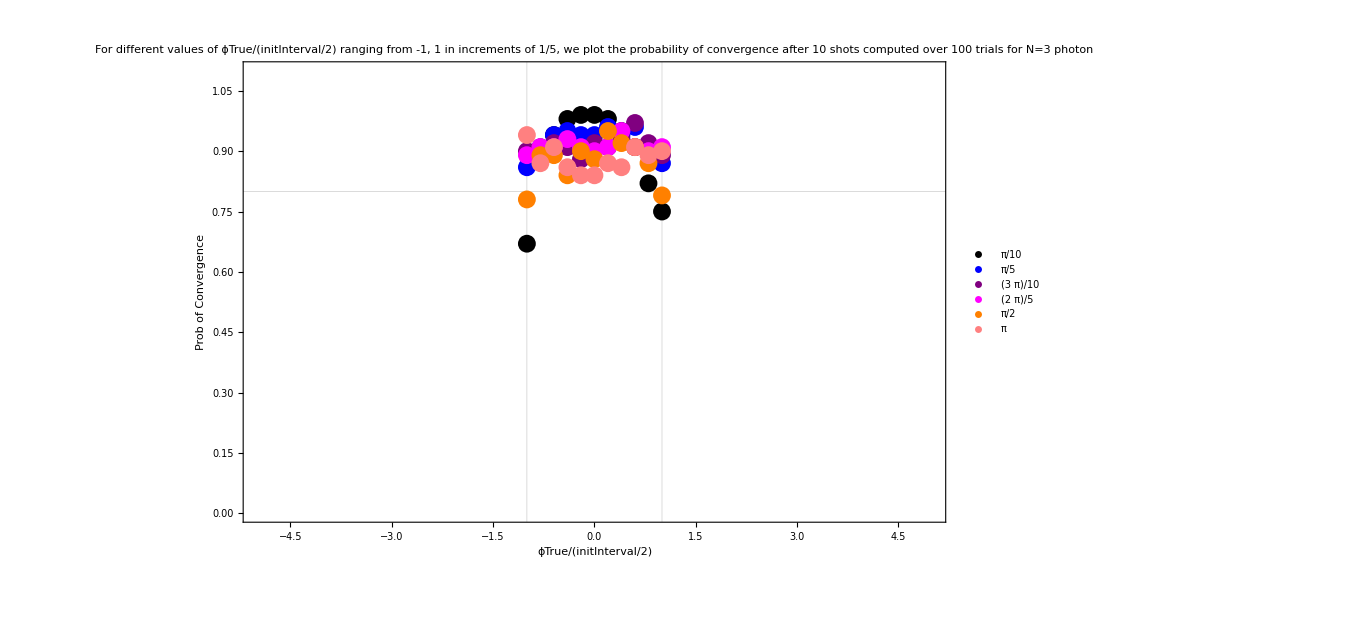

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

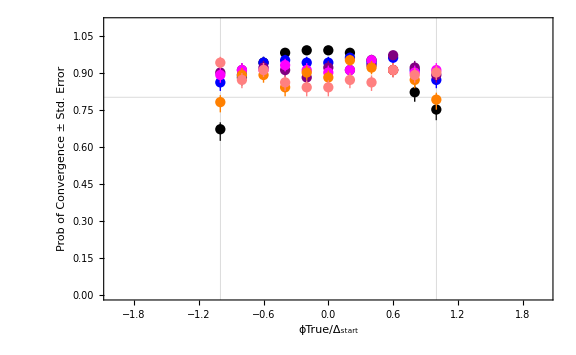

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},(*PlotLabel->"Probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",*)PlotLegends->Placed[{"Δ_start=π/10"},{Right,Center}],GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"Δ_start=(2  π)/10"},{Right,Center}]],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->Placed[{"Δ_start=(3  π)/10"},{Right,Center}]],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->Placed[{"Δ_start=(4  π)/10"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"Δ_start=(5  π)/10"},{Right,Center}]],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->Placed[{"Δ_start=π"},{Right,Center}]],PlotRange->{{-2,2},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/Δ_start",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->Large]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

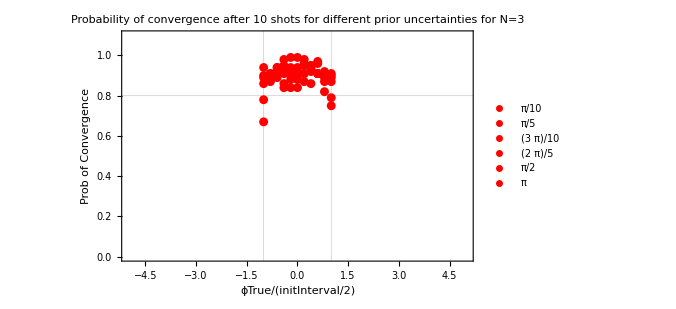

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

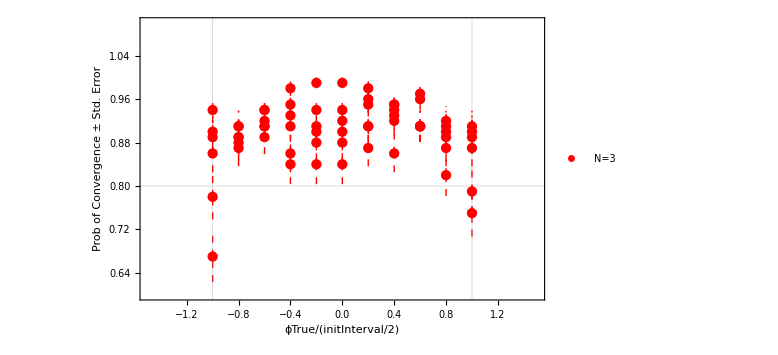

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->Placed[{"N=3"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->Large]
```

```mathematica
plot34=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
(*Average y*)
```

```mathematica
Average3y = Table[Mean[y[[1,n]]],{n,1,6}]
```

{0.896364,0.923636,0.914545,0.911818,0.874545,0.880909}

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σ=Table[ 1/11 √Sum[z1[[1,m,n]]^2,{n,1,11}],{m,1,6}]
```

{0.00865596,0.00794194,0.00840209,0.00853723,0.00987274,0.00972302}

```mathematica
(*(Subscript[y, i] Subscript[σ, i])*)
```

```mathematica
Average3=MatrixForm[Thread[{Average3y,Average3σ}]]
```

(0.896364 | 0.00865596
0.923636 | 0.00794194
0.914545 | 0.00840209
0.911818 | 0.00853723
0.874545 | 0.00987274
0.880909 | 0.00972302)

```mathematica
Average3=Table[Around[Average3[[1,n,1]],Average3[[1,n,2]]],{n,1,Length[Data]}]
```

{0.8960.009,0.9240.008,0.9150.008,0.9120.009,0.8750.010,0.8810.010}

```mathematica
(*Total Average*)
```

```mathematica
TotalAverage3y=Mean[Average3[[1,All,1]]]
```

0.900303

```mathematica
TotalAverage3σ = 1/6 √Sum[Average3[[1,n,2]]^2,{n,1,6}]
```

0.00362663

```mathematica
TotalAverage3= Around[TotalAverage3y,TotalAverage3σ]
```

0.9000.004

```mathematica
TotalAverage3=0.900.09
```

0.900.09

### Nph = 5

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=5;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data={({{-π/20, -1, 0.76, π/10}, {-π/25, -4/5, 0.9, π/10}, {-(3 π)/100, -3/5, 0.92, π/10}, {-π/50, -2/5, 0.92, π/10}, {-π/100, -1/5, 0.95, π/10}, {0, 0, 0.95, π/10}, {π/100, 1/5, 0.96, π/10}, {π/50, 2/5, 0.94, π/10}, {(3 π)/100, 3/5, 0.89, π/10}, {π/25, 4/5, 0.88, π/10}, {π/20, 1, 0.84, π/10}}),({{-π/10, -1, 0.91, π/5}, {-(2 π)/25, -4/5, 0.87, π/5}, {-(3 π)/50, -3/5, 0.88, π/5}, {-π/25, -2/5, 0.91, π/5}, {-π/50, -1/5, 0.91, π/5}, {0, 0, 0.93, π/5}, {π/50, 1/5, 0.87, π/5}, {π/25, 2/5, 0.84, π/5}, {(3 π)/50, 3/5, 0.89, π/5}, {(2 π)/25, 4/5, 0.92, π/5}, {π/10, 1, 0.88, π/5}}),({{-(3 π)/20, -1, 0.76, (3 π)/10}, {-(3 π)/25, -4/5, 0.93, (3 π)/10}, {-(9 π)/100, -3/5, 0.87, (3 π)/10}, {-(3 π)/50, -2/5, 0.91, (3 π)/10}, {-(3 π)/100, -1/5, 0.91, (3 π)/10}, {0, 0, 0.88, (3 π)/10}, {(3 π)/100, 1/5, 0.87, (3 π)/10}, {(3 π)/50, 2/5, 0.88, (3 π)/10}, {(9 π)/100, 3/5, 0.92, (3 π)/10}, {(3 π)/25, 4/5, 0.88, (3 π)/10}, {(3 π)/20, 1, 0.79, (3 π)/10}}),({{-π/5, -1, 0.86, (2 π)/5}, {-(4 π)/25, -4/5, 0.87, (2 π)/5}, {-(3 π)/25, -3/5, 0.88, (2 π)/5}, {-(2 π)/25, -2/5, 0.88, (2 π)/5}, {-π/25, -1/5, 0.88, (2 π)/5}, {0, 0, 0.95, (2 π)/5}, {π/25, 1/5, 0.91, (2 π)/5}, {(2 π)/25, 2/5, 0.87, (2 π)/5}, {(3 π)/25, 3/5, 0.83, (2 π)/5}, {(4 π)/25, 4/5, 0.87, (2 π)/5}, {π/5, 1, 0.76, (2 π)/5}}),({{-π/4, -1, 0.81, π/2}, {-π/5, -4/5, 0.82, π/2}, {-(3 π)/20, -3/5, 0.9, π/2}, {-π/10, -2/5, 0.87, π/2}, {-π/20, -1/5, 0.96, π/2}, {0, 0, 0.84, π/2}, {π/20, 1/5, 0.85, π/2}, {π/10, 2/5, 0.86, π/2}, {(3 π)/20, 3/5, 0.86, π/2}, {π/5, 4/5, 0.88, π/2}, {π/4, 1, 0.88, π/2}}),({{-π/2, -1, 0.8, π}, {-(2 π)/5, -4/5, 0.93, π}, {-(3 π)/10, -3/5, 0.89, π}, {-π/5, -2/5, 0.85, π}, {-π/10, -1/5, 0.87, π}, {0, 0, 0.86, π}, {π/10, 1/5, 0.82, π}, {π/5, 2/5, 0.91, π}, {(3 π)/10, 3/5, 0.85, π}, {(2 π)/5, 4/5, 0.91, π}, {π/2, 1, 0.83, π}})};
```

```mathematica
Data=Table[MatrixForm[Data[[n]]],{n,1,6}]
```

{(-π/20 | -1 | 0.76 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.92 | π/10
-π/50 | -2/5 | 0.92 | π/10
-π/100 | -1/5 | 0.95 | π/10
0 | 0 | 0.95 | π/10
π/100 | 1/5 | 0.96 | π/10
π/50 | 2/5 | 0.94 | π/10
(3 π)/100 | 3/5 | 0.89 | π/10
π/25 | 4/5 | 0.88 | π/10
π/20 | 1 | 0.84 | π/10),(-π/10 | -1 | 0.91 | π/5
-(2 π)/25 | -4/5 | 0.87 | π/5
-(3 π)/50 | -3/5 | 0.88 | π/5
-π/25 | -2/5 | 0.91 | π/5
-π/50 | -1/5 | 0.91 | π/5
0 | 0 | 0.93 | π/5
π/50 | 1/5 | 0.87 | π/5
π/25 | 2/5 | 0.84 | π/5
(3 π)/50 | 3/5 | 0.89 | π/5
(2 π)/25 | 4/5 | 0.92 | π/5
π/10 | 1 | 0.88 | π/5),(-(3 π)/20 | -1 | 0.76 | (3 π)/10
-(3 π)/25 | -4/5 | 0.93 | (3 π)/10
-(9 π)/100 | -3/5 | 0.87 | (3 π)/10
-(3 π)/50 | -2/5 | 0.91 | (3 π)/10
-(3 π)/100 | -1/5 | 0.91 | (3 π)/10
0 | 0 | 0.88 | (3 π)/10
(3 π)/100 | 1/5 | 0.87 | (3 π)/10
(3 π)/50 | 2/5 | 0.88 | (3 π)/10
(9 π)/100 | 3/5 | 0.92 | (3 π)/10
(3 π)/25 | 4/5 | 0.88 | (3 π)/10
(3 π)/20 | 1 | 0.79 | (3 π)/10),(-π/5 | -1 | 0.86 | (2 π)/5
-(4 π)/25 | -4/5 | 0.87 | (2 π)/5
-(3 π)/25 | -3/5 | 0.88 | (2 π)/5
-(2 π)/25 | -2/5 | 0.88 | (2 π)/5
-π/25 | -1/5 | 0.88 | (2 π)/5
0 | 0 | 0.95 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.87 | (2 π)/5
(3 π)/25 | 3/5 | 0.83 | (2 π)/5
(4 π)/25 | 4/5 | 0.87 | (2 π)/5
π/5 | 1 | 0.76 | (2 π)/5),(-π/4 | -1 | 0.81 | π/2
-π/5 | -4/5 | 0.82 | π/2
-(3 π)/20 | -3/5 | 0.9 | π/2
-π/10 | -2/5 | 0.87 | π/2
-π/20 | -1/5 | 0.96 | π/2
0 | 0 | 0.84 | π/2
π/20 | 1/5 | 0.85 | π/2
π/10 | 2/5 | 0.86 | π/2
(3 π)/20 | 3/5 | 0.86 | π/2
π/5 | 4/5 | 0.88 | π/2
π/4 | 1 | 0.88 | π/2),(-π/2 | -1 | 0.8 | π
-(2 π)/5 | -4/5 | 0.93 | π
-(3 π)/10 | -3/5 | 0.89 | π
-π/5 | -2/5 | 0.85 | π
-π/10 | -1/5 | 0.87 | π
0 | 0 | 0.86 | π
π/10 | 1/5 | 0.82 | π
π/5 | 2/5 | 0.91 | π
(3 π)/10 | 3/5 | 0.85 | π
(2 π)/5 | 4/5 | 0.91 | π
π/2 | 1 | 0.83 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.76 | 0.9 | 0.92 | 0.92 | 0.95 | 0.95 | 0.96 | 0.94 | 0.89 | 0.88 | 0.84
0.91 | 0.87 | 0.88 | 0.91 | 0.91 | 0.93 | 0.87 | 0.84 | 0.89 | 0.92 | 0.88
0.76 | 0.93 | 0.87 | 0.91 | 0.91 | 0.88 | 0.87 | 0.88 | 0.92 | 0.88 | 0.79
0.86 | 0.87 | 0.88 | 0.88 | 0.88 | 0.95 | 0.91 | 0.87 | 0.83 | 0.87 | 0.76
0.81 | 0.82 | 0.9 | 0.87 | 0.96 | 0.84 | 0.85 | 0.86 | 0.86 | 0.88 | 0.88
0.8 | 0.93 | 0.89 | 0.85 | 0.87 | 0.86 | 0.82 | 0.91 | 0.85 | 0.91 | 0.83)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z1=MatrixForm[Table[Table[√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial),{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.0427083 | 0.03 | 0.0271293 | 0.0271293 | 0.0217945 | 0.0217945 | 0.0195959 | 0.0237487 | 0.031289 | 0.0324962 | 0.0366606
0.0286182 | 0.0336303 | 0.0324962 | 0.0286182 | 0.0286182 | 0.0255147 | 0.0336303 | 0.0366606 | 0.031289 | 0.0271293 | 0.0324962
0.0427083 | 0.0255147 | 0.0336303 | 0.0286182 | 0.0286182 | 0.0324962 | 0.0336303 | 0.0324962 | 0.0271293 | 0.0324962 | 0.0407308
0.0346987 | 0.0336303 | 0.0324962 | 0.0324962 | 0.0324962 | 0.0217945 | 0.0286182 | 0.0336303 | 0.0375633 | 0.0336303 | 0.0427083
0.0392301 | 0.0384187 | 0.03 | 0.0336303 | 0.0195959 | 0.0366606 | 0.0357071 | 0.0346987 | 0.0346987 | 0.0324962 | 0.0324962
0.04 | 0.0255147 | 0.031289 | 0.0357071 | 0.0336303 | 0.0346987 | 0.0384187 | 0.0286182 | 0.0357071 | 0.0286182 | 0.0375633)

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.760.04 | 0.9000.030 | 0.9200.027 | 0.9200.027 | 0.9500.022 | 0.9500.022 | 0.9600.020 | 0.9400.024 | 0.8900.031 | 0.8800.032 | 0.840.04
0.9100.029 | 0.8700.034 | 0.8800.032 | 0.9100.029 | 0.9100.029 | 0.9300.026 | 0.8700.034 | 0.840.04 | 0.8900.031 | 0.9200.027 | 0.8800.032
0.760.04 | 0.9300.026 | 0.8700.034 | 0.9100.029 | 0.9100.029 | 0.8800.032 | 0.8700.034 | 0.8800.032 | 0.9200.027 | 0.8800.032 | 0.790.04
0.8600.035 | 0.8700.034 | 0.8800.032 | 0.8800.032 | 0.8800.032 | 0.9500.022 | 0.9100.029 | 0.8700.034 | 0.830.04 | 0.8700.034 | 0.760.04
0.810.04 | 0.820.04 | 0.9000.030 | 0.8700.034 | 0.9600.020 | 0.840.04 | 0.850.04 | 0.8600.035 | 0.8600.035 | 0.8800.032 | 0.8800.032
0.800.04 | 0.9300.026 | 0.8900.031 | 0.850.04 | 0.8700.034 | 0.8600.035 | 0.820.04 | 0.9100.029 | 0.850.04 | 0.9100.029 | 0.830.04)

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.76) | (-4/5
0.9) | (-3/5
0.92) | (-2/5
0.92) | (-1/5
0.95) | (0
0.95) | (1/5
0.96) | (2/5
0.94) | (3/5
0.89) | (4/5
0.88) | (1
0.84)
(-1
0.91) | (-4/5
0.87) | (-3/5
0.88) | (-2/5
0.91) | (-1/5
0.91) | (0
0.93) | (1/5
0.87) | (2/5
0.84) | (3/5
0.89) | (4/5
0.92) | (1
0.88)
(-1
0.76) | (-4/5
0.93) | (-3/5
0.87) | (-2/5
0.91) | (-1/5
0.91) | (0
0.88) | (1/5
0.87) | (2/5
0.88) | (3/5
0.92) | (4/5
0.88) | (1
0.79)
(-1
0.86) | (-4/5
0.87) | (-3/5
0.88) | (-2/5
0.88) | (-1/5
0.88) | (0
0.95) | (1/5
0.91) | (2/5
0.87) | (3/5
0.83) | (4/5
0.87) | (1
0.76)
(-1
0.81) | (-4/5
0.82) | (-3/5
0.9) | (-2/5
0.87) | (-1/5
0.96) | (0
0.84) | (1/5
0.85) | (2/5
0.86) | (3/5
0.86) | (4/5
0.88) | (1
0.88)
(-1
0.8) | (-4/5
0.93) | (-3/5
0.89) | (-2/5
0.85) | (-1/5
0.87) | (0
0.86) | (1/5
0.82) | (2/5
0.91) | (3/5
0.85) | (4/5
0.91) | (1
0.83))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.760.04) | (-4/5
0.9000.030) | (-3/5
0.9200.027) | (-2/5
0.9200.027) | (-1/5
0.9500.022) | (0
0.9500.022) | (1/5
0.9600.020) | (2/5
0.9400.024) | (3/5
0.8900.031) | (4/5
0.8800.032) | (1
0.840.04)
(-1
0.9100.029) | (-4/5
0.8700.034) | (-3/5
0.8800.032) | (-2/5
0.9100.029) | (-1/5
0.9100.029) | (0
0.9300.026) | (1/5
0.8700.034) | (2/5
0.840.04) | (3/5
0.8900.031) | (4/5
0.9200.027) | (1
0.8800.032)
(-1
0.760.04) | (-4/5
0.9300.026) | (-3/5
0.8700.034) | (-2/5
0.9100.029) | (-1/5
0.9100.029) | (0
0.8800.032) | (1/5
0.8700.034) | (2/5
0.8800.032) | (3/5
0.9200.027) | (4/5
0.8800.032) | (1
0.790.04)
(-1
0.8600.035) | (-4/5
0.8700.034) | (-3/5
0.8800.032) | (-2/5
0.8800.032) | (-1/5
0.8800.032) | (0
0.9500.022) | (1/5
0.9100.029) | (2/5
0.8700.034) | (3/5
0.830.04) | (4/5
0.8700.034) | (1
0.760.04)
(-1
0.810.04) | (-4/5
0.820.04) | (-3/5
0.9000.030) | (-2/5
0.8700.034) | (-1/5
0.9600.020) | (0
0.840.04) | (1/5
0.850.04) | (2/5
0.8600.035) | (3/5
0.8600.035) | (4/5
0.8800.032) | (1
0.8800.032)
(-1
0.800.04) | (-4/5
0.9300.026) | (-3/5
0.8900.031) | (-2/5
0.850.04) | (-1/5
0.8700.034) | (0
0.8600.035) | (1/5
0.820.04) | (2/5
0.9100.029) | (3/5
0.850.04) | (4/5
0.9100.029) | (1
0.830.04))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

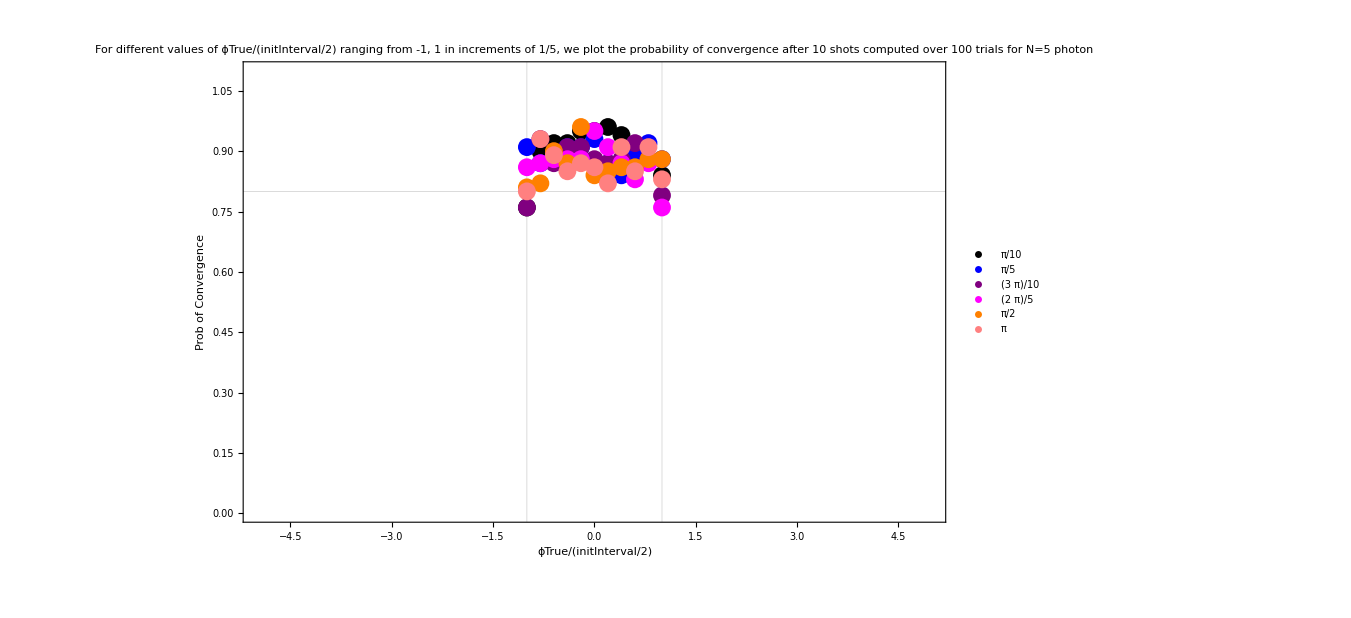

```mathematica
plot51=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=5 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

```mathematica
(*For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=5 photons*)
```

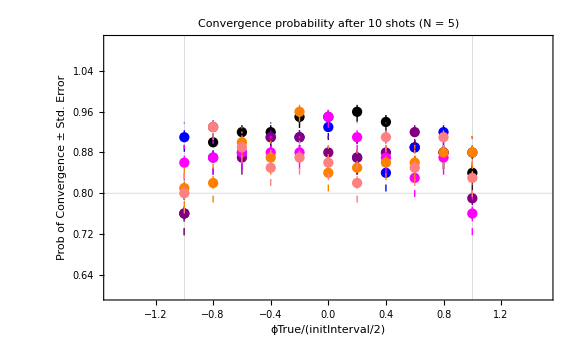

```mathematica
plot52=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"Convergence probability after 10 shots (N = 5)",PlotLegends->Placed[{π/10},{Right,Center}],GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{(2π)/10},{Right,Center}]],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->Placed[{(3π)/10},{Right,Center}]],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->Placed[{(4π)/10},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->Placed[{(5π)/10},{Right,Center}]],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->Placed[{π},{Right,Center}]],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->Large]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

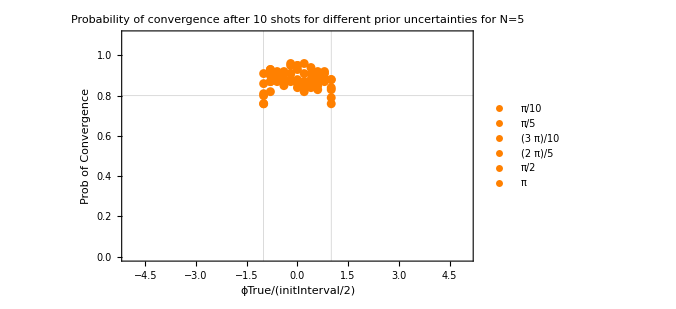

```mathematica
plot53=Show[ListPlot[plot[[1,1]],PlotStyle->{Orange, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=5",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Orange,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Orange, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Orange,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Orange,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

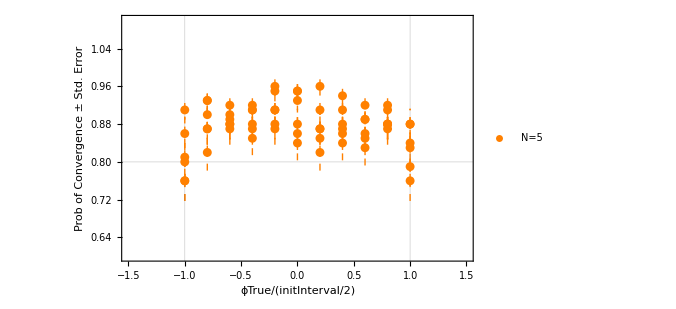

```mathematica
plot54=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Orange, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Orange,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Orange, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"N=5"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Orange,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

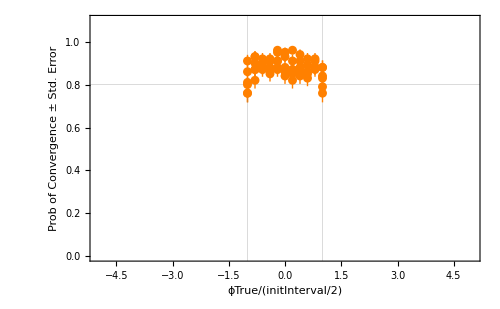
```mathematica
plot54=-Graphics-
```

-Graphics-

#### Average Error

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
(*Average y*)
```

```mathematica
Average5y = Table[Mean[y[[1,n]]],{n,1,6}]
```

{0.900909,0.891818,0.872727,0.869091,0.866364,0.865455}

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average5σ=Table[ 1/11 √Sum[z1[[1,m,n]]^2,{n,1,11}],{m,1,6}]
```

{0.00884812,0.00933358,0.00993283,0.0100798,0.010192,0.0102207}

```mathematica
(*(Subscript[y, i] Subscript[σ, i])*)
```

```mathematica
Average5=MatrixForm[Thread[{Average5y,Average5σ}]]
```

(0.900909 | 0.00884812
0.891818 | 0.00933358
0.872727 | 0.00993283
0.869091 | 0.0100798
0.866364 | 0.010192
0.865455 | 0.0102207)

```mathematica
Average5=Table[Around[Average5[[1,n,1]],Average5[[1,n,2]]],{n,1,Length[Data]}]
```

{0.9010.009,0.8920.009,0.8730.010,0.8690.010,0.8660.010,0.8650.010}

```mathematica
(*Total Average*)
```

```mathematica
TotalAverage5y=Mean[Average5[[1,All,1]]]
```

0.877727

```mathematica
TotalAverage5σ = 1/6 √Sum[Average5[[1,n,2]]^2,{n,1,6}]
```

0.00399308

```mathematica
TotalAverage5= Around[TotalAverage5y,TotalAverage5σ]
```

0.8780.004

```mathematica
TotalAverage5=0.880.09
```

0.880.09

### Nph = 7

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=7;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data={({{-π/20, -1, 0.89, π/10}, {-π/25, -4/5, 0.9, π/10}, {-(3 π)/100, -3/5, 0.89, π/10}, {-π/50, -2/5, 0.93, π/10}, {-π/100, -1/5, 0.94, π/10}, {0, 0, 0.95, π/10}, {π/100, 1/5, 0.89, π/10}, {π/50, 2/5, 0.91, π/10}, {(3 π)/100, 3/5, 0.84, π/10}, {π/25, 4/5, 0.83, π/10}, {π/20, 1, 0.88, π/10}}),({{-π/10, -1, 0.79, π/5}, {-(2 π)/25, -4/5, 0.93, π/5}, {-(3 π)/50, -3/5, 0.88, π/5}, {-π/25, -2/5, 0.93, π/5}, {-π/50, -1/5, 0.88, π/5}, {0, 0, 0.86, π/5}, {π/50, 1/5, 0.89, π/5}, {π/25, 2/5, 0.93, π/5}, {(3 π)/50, 3/5, 0.93, π/5}, {(2 π)/25, 4/5, 0.88, π/5}, {π/10, 1, 0.82, π/5}}),({{-(3 π)/20, -1, 0.8, (3 π)/10}, {-(3 π)/25, -4/5, 0.9, (3 π)/10}, {-(9 π)/100, -3/5, 0.83, (3 π)/10}, {-(3 π)/50, -2/5, 0.89, (3 π)/10}, {-(3 π)/100, -1/5, 0.89, (3 π)/10}, {0, 0, 0.88, (3 π)/10}, {(3 π)/100, 1/5, 0.9, (3 π)/10}, {(3 π)/50, 2/5, 0.87, (3 π)/10}, {(9 π)/100, 3/5, 0.82, (3 π)/10}, {(3 π)/25, 4/5, 0.87, (3 π)/10}, {(3 π)/20, 1, 0.83, (3 π)/10}}),({{-π/5, -1, 0.82, (2 π)/5}, {-(4 π)/25, -4/5, 0.85, (2 π)/5}, {-(3 π)/25, -3/5, 0.81, (2 π)/5}, {-(2 π)/25, -2/5, 0.86, (2 π)/5}, {-π/25, -1/5, 0.87, (2 π)/5}, {0, 0, 0.84, (2 π)/5}, {π/25, 1/5, 0.91, (2 π)/5}, {(2 π)/25, 2/5, 0.84, (2 π)/5}, {(3 π)/25, 3/5, 0.86, (2 π)/5}, {(4 π)/25, 4/5, 0.87, (2 π)/5}, {π/5, 1, 0.77, (2 π)/5}}),({{-π/4, -1, 0.89, π/2}, {-π/5, -4/5, 0.86, π/2}, {-(3 π)/20, -3/5, 0.9, π/2}, {-π/10, -2/5, 0.91, π/2}, {-π/20, -1/5, 0.85, π/2}, {0, 0, 0.88, π/2}, {π/20, 1/5, 0.89, π/2}, {π/10, 2/5, 0.91, π/2}, {(3 π)/20, 3/5, 0.86, π/2}, {π/5, 4/5, 0.78, π/2}, {π/4, 1, 0.8, π/2}}),({{-π/2, -1, 0.84, π}, {-(2 π)/5, -4/5, 0.88, π}, {-(3 π)/10, -3/5, 0.89, π}, {-π/5, -2/5, 0.88, π}, {-π/10, -1/5, 0.84, π}, {0, 0, 0.78, π}, {π/10, 1/5, 0.82, π}, {π/5, 2/5, 0.87, π}, {(3 π)/10, 3/5, 0.85, π}, {(2 π)/5, 4/5, 0.89, π}, {π/2, 1, 0.86, π}})};
```

```mathematica
Data=Table[MatrixForm[Data[[n]]],{n,1,6}]
```

{(-π/20 | -1 | 0.89 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.89 | π/10
-π/50 | -2/5 | 0.93 | π/10
-π/100 | -1/5 | 0.94 | π/10
0 | 0 | 0.95 | π/10
π/100 | 1/5 | 0.89 | π/10
π/50 | 2/5 | 0.91 | π/10
(3 π)/100 | 3/5 | 0.84 | π/10
π/25 | 4/5 | 0.83 | π/10
π/20 | 1 | 0.88 | π/10),(-π/10 | -1 | 0.79 | π/5
-(2 π)/25 | -4/5 | 0.93 | π/5
-(3 π)/50 | -3/5 | 0.88 | π/5
-π/25 | -2/5 | 0.93 | π/5
-π/50 | -1/5 | 0.88 | π/5
0 | 0 | 0.86 | π/5
π/50 | 1/5 | 0.89 | π/5
π/25 | 2/5 | 0.93 | π/5
(3 π)/50 | 3/5 | 0.93 | π/5
(2 π)/25 | 4/5 | 0.88 | π/5
π/10 | 1 | 0.82 | π/5),(-(3 π)/20 | -1 | 0.8 | (3 π)/10
-(3 π)/25 | -4/5 | 0.9 | (3 π)/10
-(9 π)/100 | -3/5 | 0.83 | (3 π)/10
-(3 π)/50 | -2/5 | 0.89 | (3 π)/10
-(3 π)/100 | -1/5 | 0.89 | (3 π)/10
0 | 0 | 0.88 | (3 π)/10
(3 π)/100 | 1/5 | 0.9 | (3 π)/10
(3 π)/50 | 2/5 | 0.87 | (3 π)/10
(9 π)/100 | 3/5 | 0.82 | (3 π)/10
(3 π)/25 | 4/5 | 0.87 | (3 π)/10
(3 π)/20 | 1 | 0.83 | (3 π)/10),(-π/5 | -1 | 0.82 | (2 π)/5
-(4 π)/25 | -4/5 | 0.85 | (2 π)/5
-(3 π)/25 | -3/5 | 0.81 | (2 π)/5
-(2 π)/25 | -2/5 | 0.86 | (2 π)/5
-π/25 | -1/5 | 0.87 | (2 π)/5
0 | 0 | 0.84 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.84 | (2 π)/5
(3 π)/25 | 3/5 | 0.86 | (2 π)/5
(4 π)/25 | 4/5 | 0.87 | (2 π)/5
π/5 | 1 | 0.77 | (2 π)/5),(-π/4 | -1 | 0.89 | π/2
-π/5 | -4/5 | 0.86 | π/2
-(3 π)/20 | -3/5 | 0.9 | π/2
-π/10 | -2/5 | 0.91 | π/2
-π/20 | -1/5 | 0.85 | π/2
0 | 0 | 0.88 | π/2
π/20 | 1/5 | 0.89 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.86 | π/2
π/5 | 4/5 | 0.78 | π/2
π/4 | 1 | 0.8 | π/2),(-π/2 | -1 | 0.84 | π
-(2 π)/5 | -4/5 | 0.88 | π
-(3 π)/10 | -3/5 | 0.89 | π
-π/5 | -2/5 | 0.88 | π
-π/10 | -1/5 | 0.84 | π
0 | 0 | 0.78 | π
π/10 | 1/5 | 0.82 | π
π/5 | 2/5 | 0.87 | π
(3 π)/10 | 3/5 | 0.85 | π
(2 π)/5 | 4/5 | 0.89 | π
π/2 | 1 | 0.86 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.89 | 0.9 | 0.89 | 0.93 | 0.94 | 0.95 | 0.89 | 0.91 | 0.84 | 0.83 | 0.88
0.79 | 0.93 | 0.88 | 0.93 | 0.88 | 0.86 | 0.89 | 0.93 | 0.93 | 0.88 | 0.82
0.8 | 0.9 | 0.83 | 0.89 | 0.89 | 0.88 | 0.9 | 0.87 | 0.82 | 0.87 | 0.83
0.82 | 0.85 | 0.81 | 0.86 | 0.87 | 0.84 | 0.91 | 0.84 | 0.86 | 0.87 | 0.77
0.89 | 0.86 | 0.9 | 0.91 | 0.85 | 0.88 | 0.89 | 0.91 | 0.86 | 0.78 | 0.8
0.84 | 0.88 | 0.89 | 0.88 | 0.84 | 0.78 | 0.82 | 0.87 | 0.85 | 0.89 | 0.86)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z1=MatrixForm[Table[Table[√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial),{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.031289 | 0.03 | 0.031289 | 0.0255147 | 0.0237487 | 0.0217945 | 0.031289 | 0.0286182 | 0.0366606 | 0.0375633 | 0.0324962
0.0407308 | 0.0255147 | 0.0324962 | 0.0255147 | 0.0324962 | 0.0346987 | 0.031289 | 0.0255147 | 0.0255147 | 0.0324962 | 0.0384187
0.04 | 0.03 | 0.0375633 | 0.031289 | 0.031289 | 0.0324962 | 0.03 | 0.0336303 | 0.0384187 | 0.0336303 | 0.0375633
0.0384187 | 0.0357071 | 0.0392301 | 0.0346987 | 0.0336303 | 0.0366606 | 0.0286182 | 0.0366606 | 0.0346987 | 0.0336303 | 0.0420833
0.031289 | 0.0346987 | 0.03 | 0.0286182 | 0.0357071 | 0.0324962 | 0.031289 | 0.0286182 | 0.0346987 | 0.0414246 | 0.04
0.0366606 | 0.0324962 | 0.031289 | 0.0324962 | 0.0366606 | 0.0414246 | 0.0384187 | 0.0336303 | 0.0357071 | 0.031289 | 0.0346987)

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.8900.031 | 0.9000.030 | 0.8900.031 | 0.9300.026 | 0.9400.024 | 0.9500.022 | 0.8900.031 | 0.9100.029 | 0.840.04 | 0.830.04 | 0.8800.032
0.790.04 | 0.9300.026 | 0.8800.032 | 0.9300.026 | 0.8800.032 | 0.8600.035 | 0.8900.031 | 0.9300.026 | 0.9300.026 | 0.8800.032 | 0.820.04
0.800.04 | 0.9000.030 | 0.830.04 | 0.8900.031 | 0.8900.031 | 0.8800.032 | 0.9000.030 | 0.8700.034 | 0.820.04 | 0.8700.034 | 0.830.04
0.820.04 | 0.850.04 | 0.810.04 | 0.8600.035 | 0.8700.034 | 0.840.04 | 0.9100.029 | 0.840.04 | 0.8600.035 | 0.8700.034 | 0.770.04
0.8900.031 | 0.8600.035 | 0.9000.030 | 0.9100.029 | 0.850.04 | 0.8800.032 | 0.8900.031 | 0.9100.029 | 0.8600.035 | 0.780.04 | 0.800.04
0.840.04 | 0.8800.032 | 0.8900.031 | 0.8800.032 | 0.840.04 | 0.780.04 | 0.820.04 | 0.8700.034 | 0.850.04 | 0.8900.031 | 0.8600.035)

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.89) | (-4/5
0.9) | (-3/5
0.89) | (-2/5
0.93) | (-1/5
0.94) | (0
0.95) | (1/5
0.89) | (2/5
0.91) | (3/5
0.84) | (4/5
0.83) | (1
0.88)
(-1
0.79) | (-4/5
0.93) | (-3/5
0.88) | (-2/5
0.93) | (-1/5
0.88) | (0
0.86) | (1/5
0.89) | (2/5
0.93) | (3/5
0.93) | (4/5
0.88) | (1
0.82)
(-1
0.8) | (-4/5
0.9) | (-3/5
0.83) | (-2/5
0.89) | (-1/5
0.89) | (0
0.88) | (1/5
0.9) | (2/5
0.87) | (3/5
0.82) | (4/5
0.87) | (1
0.83)
(-1
0.82) | (-4/5
0.85) | (-3/5
0.81) | (-2/5
0.86) | (-1/5
0.87) | (0
0.84) | (1/5
0.91) | (2/5
0.84) | (3/5
0.86) | (4/5
0.87) | (1
0.77)
(-1
0.89) | (-4/5
0.86) | (-3/5
0.9) | (-2/5
0.91) | (-1/5
0.85) | (0
0.88) | (1/5
0.89) | (2/5
0.91) | (3/5
0.86) | (4/5
0.78) | (1
0.8)
(-1
0.84) | (-4/5
0.88) | (-3/5
0.89) | (-2/5
0.88) | (-1/5
0.84) | (0
0.78) | (1/5
0.82) | (2/5
0.87) | (3/5
0.85) | (4/5
0.89) | (1
0.86))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.8900.031) | (-4/5
0.9000.030) | (-3/5
0.8900.031) | (-2/5
0.9300.026) | (-1/5
0.9400.024) | (0
0.9500.022) | (1/5
0.8900.031) | (2/5
0.9100.029) | (3/5
0.840.04) | (4/5
0.830.04) | (1
0.8800.032)
(-1
0.790.04) | (-4/5
0.9300.026) | (-3/5
0.8800.032) | (-2/5
0.9300.026) | (-1/5
0.8800.032) | (0
0.8600.035) | (1/5
0.8900.031) | (2/5
0.9300.026) | (3/5
0.9300.026) | (4/5
0.8800.032) | (1
0.820.04)
(-1
0.800.04) | (-4/5
0.9000.030) | (-3/5
0.830.04) | (-2/5
0.8900.031) | (-1/5
0.8900.031) | (0
0.8800.032) | (1/5
0.9000.030) | (2/5
0.8700.034) | (3/5
0.820.04) | (4/5
0.8700.034) | (1
0.830.04)
(-1
0.820.04) | (-4/5
0.850.04) | (-3/5
0.810.04) | (-2/5
0.8600.035) | (-1/5
0.8700.034) | (0
0.840.04) | (1/5
0.9100.029) | (2/5
0.840.04) | (3/5
0.8600.035) | (4/5
0.8700.034) | (1
0.770.04)
(-1
0.8900.031) | (-4/5
0.8600.035) | (-3/5
0.9000.030) | (-2/5
0.9100.029) | (-1/5
0.850.04) | (0
0.8800.032) | (1/5
0.8900.031) | (2/5
0.9100.029) | (3/5
0.8600.035) | (4/5
0.780.04) | (1
0.800.04)
(-1
0.840.04) | (-4/5
0.8800.032) | (-3/5
0.8900.031) | (-2/5
0.8800.032) | (-1/5
0.840.04) | (0
0.780.04) | (1/5
0.820.04) | (2/5
0.8700.034) | (3/5
0.850.04) | (4/5
0.8900.031) | (1
0.8600.035))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

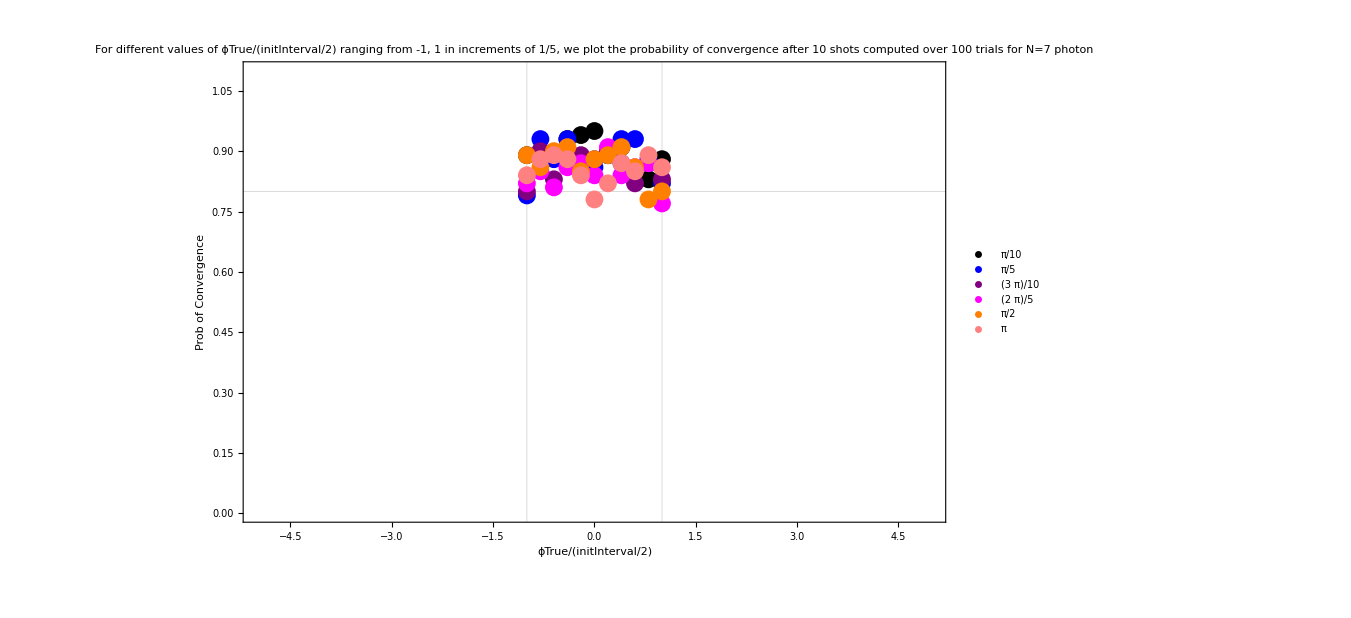

```mathematica
plot71=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=7 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

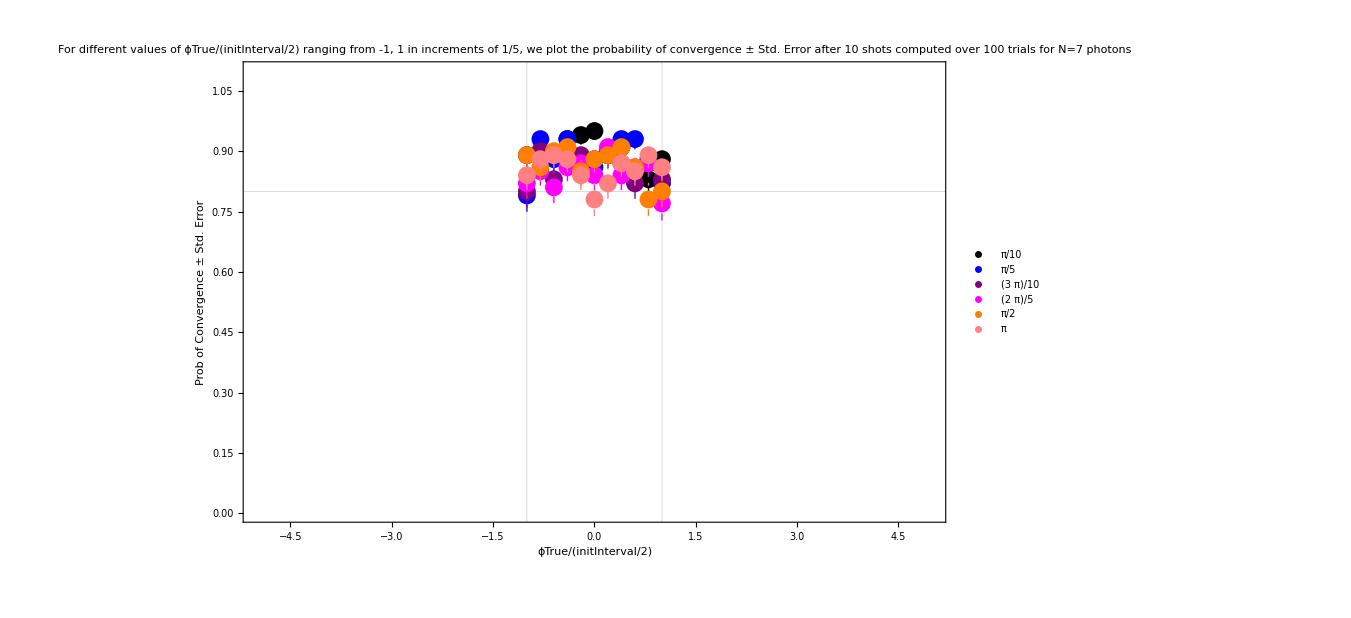

```mathematica
plot72=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=7 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

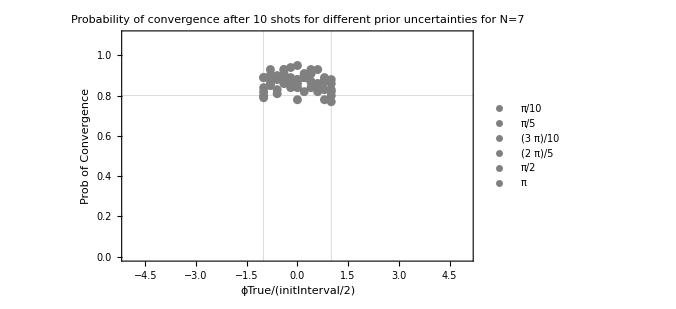

```mathematica
plot73=Show[ListPlot[plot[[1,1]],PlotStyle->{Gray, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=7",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Gray,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Gray, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Gray,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Gray,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Gray,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

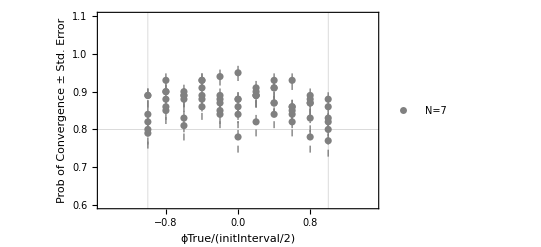

```mathematica
plot74=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Gray, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Gray, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"N=7"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Gray,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

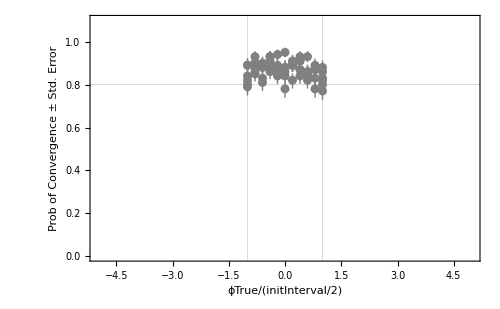
```mathematica
plot74=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
z1
```

((0.89
0.031289) | (0.9
0.03) | (0.89
0.031289) | (0.93
0.0255147) | (0.94
0.0237487) | (0.95
0.0217945) | (0.89
0.031289) | (0.91
0.0286182) | (0.84
0.0366606) | (0.83
0.0375633) | (0.88
0.0324962)
(0.79
0.0407308) | (0.93
0.0255147) | (0.88
0.0324962) | (0.93
0.0255147) | (0.88
0.0324962) | (0.86
0.0346987) | (0.89
0.031289) | (0.93
0.0255147) | (0.93
0.0255147) | (0.88
0.0324962) | (0.82
0.0384187)
(0.8
0.04) | (0.9
0.03) | (0.83
0.0375633) | (0.89
0.031289) | (0.89
0.031289) | (0.88
0.0324962) | (0.9
0.03) | (0.87
0.0336303) | (0.82
0.0384187) | (0.87
0.0336303) | (0.83
0.0375633)
(0.82
0.0384187) | (0.85
0.0357071) | (0.81
0.0392301) | (0.86
0.0346987) | (0.87
0.0336303) | (0.84
0.0366606) | (0.91
0.0286182) | (0.84
0.0366606) | (0.86
0.0346987) | (0.87
0.0336303) | (0.77
0.0420833)
(0.89
0.031289) | (0.86
0.0346987) | (0.9
0.03) | (0.91
0.0286182) | (0.85
0.0357071) | (0.88
0.0324962) | (0.89
0.031289) | (0.91
0.0286182) | (0.86
0.0346987) | (0.78
0.0414246) | (0.8
0.04)
(0.84
0.0366606) | (0.88
0.0324962) | (0.89
0.031289) | (0.88
0.0324962) | (0.84
0.0366606) | (0.78
0.0414246) | (0.82
0.0384187) | (0.87
0.0336303) | (0.85
0.0357071) | (0.89
0.031289) | (0.86
0.0346987))

```mathematica
Average7=Table[MatrixForm[Mean[z1[[1,n]]]],{n,1,Length[Data]}]
```

{(0.895455
0.0300239),(0.883636
0.031335),(0.861818
0.0341709),(0.845455
0.0358215),(0.866364
0.0335309),(0.854545
0.0349792)}

```mathematica
Around[Mean[Table[Average7[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average7[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8680.033

```mathematica
Average7=0.8680.033
```

0.8680.033

#### Average Error

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
(*Average y*)
```

```mathematica
Average7y = Table[Mean[y[[1,n]]],{n,1,6}]
```

{0.895455,0.883636,0.861818,0.845455,0.866364,0.854545}

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average7σ=Table[ 1/11 √Sum[z1[[1,m,n]]^2,{n,1,11}],{m,1,6}]
```

{0.00916199,0.00957355,0.0103549,0.0108476,0.0101847,0.0105861}

```mathematica
(*(Subscript[y, i] Subscript[σ, i])*)
```

```mathematica
Average7=MatrixForm[Thread[{Average7y,Average7σ}]]
```

(0.895455 | 0.00916199
0.883636 | 0.00957355
0.861818 | 0.0103549
0.845455 | 0.0108476
0.866364 | 0.0101847
0.854545 | 0.0105861)

```mathematica
Average7=Table[Around[Average7[[1,n,1]],Average7[[1,n,2]]],{n,1,Length[Data]}]
```

{0.8950.009,0.8840.010,0.8620.010,0.8450.011,0.8660.010,0.8550.011}

```mathematica
(*Total Average*)
```

```mathematica
TotalAverage7y=Mean[Average7[[1,All,1]]]
```

0.867879

```mathematica
TotalAverage7σ = 1/6 √Sum[Average7[[1,n,2]]^2,{n,1,6}]
```

0.0041375

```mathematica
TotalAverage7= Around[TotalAverage7y,TotalAverage7σ]
```

0.8680.004

### Nph = 10

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data={({{-π/20, -1, 0.86, π/10}, {-π/25, -4/5, 0.94, π/10}, {-(3 π)/100, -3/5, 0.85, π/10}, {-π/50, -2/5, 0.91, π/10}, {-π/100, -1/5, 0.93, π/10}, {0, 0, 0.94, π/10}, {π/100, 1/5, 0.94, π/10}, {π/50, 2/5, 0.92, π/10}, {(3 π)/100, 3/5, 0.93, π/10}, {π/25, 4/5, 0.92, π/10}, {π/20, 1, 0.88, π/10}}),({{-π/10, -1, 0.86, π/5}, {-(2 π)/25, -4/5, 0.87, π/5}, {-(3 π)/50, -3/5, 0.92, π/5}, {-π/25, -2/5, 0.9, π/5}, {-π/50, -1/5, 0.89, π/5}, {0, 0, 0.97, π/5}, {π/50, 1/5, 0.86, π/5}, {π/25, 2/5, 0.93, π/5}, {(3 π)/50, 3/5, 0.89, π/5}, {(2 π)/25, 4/5, 0.83, π/5}, {π/10, 1, 0.83, π/5}}),({{-(3 π)/20, -1, 0.85, (3 π)/10}, {-(3 π)/25, -4/5, 0.84, (3 π)/10}, {-(9 π)/100, -3/5, 0.84, (3 π)/10}, {-(3 π)/50, -2/5, 0.92, (3 π)/10}, {-(3 π)/100, -1/5, 0.88, (3 π)/10}, {0, 0, 0.87, (3 π)/10}, {(3 π)/100, 1/5, 0.87, (3 π)/10}, {(3 π)/50, 2/5, 0.92, (3 π)/10}, {(9 π)/100, 3/5, 0.89, (3 π)/10}, {(3 π)/25, 4/5, 0.88, (3 π)/10}, {(3 π)/20, 1, 0.85, (3 π)/10}}),({{-π/5, -1, 0.87, (2 π)/5}, {-(4 π)/25, -4/5, 0.92, (2 π)/5}, {-(3 π)/25, -3/5, 0.87, (2 π)/5}, {-(2 π)/25, -2/5, 0.89, (2 π)/5}, {-π/25, -1/5, 0.87, (2 π)/5}, {0, 0, 0.87, (2 π)/5}, {π/25, 1/5, 0.9, (2 π)/5}, {(2 π)/25, 2/5, 0.92, (2 π)/5}, {(3 π)/25, 3/5, 0.88, (2 π)/5}, {(4 π)/25, 4/5, 0.9, (2 π)/5}, {π/5, 1, 0.84, (2 π)/5}}),({{-π/4, -1, 0.81, π/2}, {-π/5, -4/5, 0.93, π/2}, {-(3 π)/20, -3/5, 0.86, π/2}, {-π/10, -2/5, 0.83, π/2}, {-π/20, -1/5, 0.9, π/2}, {0, 0, 0.88, π/2}, {π/20, 1/5, 0.88, π/2}, {π/10, 2/5, 0.91, π/2}, {(3 π)/20, 3/5, 0.84, π/2}, {π/5, 4/5, 0.86, π/2}, {π/4, 1, 0.87, π/2}}),({{-π/2, -1, 0.84, π}, {-(2 π)/5, -4/5, 0.83, π}, {-(3 π)/10, -3/5, 0.87, π}, {-π/5, -2/5, 0.88, π}, {-π/10, -1/5, 0.9, π}, {0, 0, 0.85, π}, {π/10, 1/5, 0.87, π}, {π/5, 2/5, 0.87, π}, {(3 π)/10, 3/5, 0.86, π}, {(2 π)/5, 4/5, 0.9, π}, {π/2, 1, 0.83, π}})};
```

```mathematica
Data=Table[MatrixForm[Data[[n]]],{n,1,6}]
```

{(-π/20 | -1 | 0.86 | π/10
-π/25 | -4/5 | 0.94 | π/10
-(3 π)/100 | -3/5 | 0.85 | π/10
-π/50 | -2/5 | 0.91 | π/10
-π/100 | -1/5 | 0.93 | π/10
0 | 0 | 0.94 | π/10
π/100 | 1/5 | 0.94 | π/10
π/50 | 2/5 | 0.92 | π/10
(3 π)/100 | 3/5 | 0.93 | π/10
π/25 | 4/5 | 0.92 | π/10
π/20 | 1 | 0.88 | π/10),(-π/10 | -1 | 0.86 | π/5
-(2 π)/25 | -4/5 | 0.87 | π/5
-(3 π)/50 | -3/5 | 0.92 | π/5
-π/25 | -2/5 | 0.9 | π/5
-π/50 | -1/5 | 0.89 | π/5
0 | 0 | 0.97 | π/5
π/50 | 1/5 | 0.86 | π/5
π/25 | 2/5 | 0.93 | π/5
(3 π)/50 | 3/5 | 0.89 | π/5
(2 π)/25 | 4/5 | 0.83 | π/5
π/10 | 1 | 0.83 | π/5),(-(3 π)/20 | -1 | 0.85 | (3 π)/10
-(3 π)/25 | -4/5 | 0.84 | (3 π)/10
-(9 π)/100 | -3/5 | 0.84 | (3 π)/10
-(3 π)/50 | -2/5 | 0.92 | (3 π)/10
-(3 π)/100 | -1/5 | 0.88 | (3 π)/10
0 | 0 | 0.87 | (3 π)/10
(3 π)/100 | 1/5 | 0.87 | (3 π)/10
(3 π)/50 | 2/5 | 0.92 | (3 π)/10
(9 π)/100 | 3/5 | 0.89 | (3 π)/10
(3 π)/25 | 4/5 | 0.88 | (3 π)/10
(3 π)/20 | 1 | 0.85 | (3 π)/10),(-π/5 | -1 | 0.87 | (2 π)/5
-(4 π)/25 | -4/5 | 0.92 | (2 π)/5
-(3 π)/25 | -3/5 | 0.87 | (2 π)/5
-(2 π)/25 | -2/5 | 0.89 | (2 π)/5
-π/25 | -1/5 | 0.87 | (2 π)/5
0 | 0 | 0.87 | (2 π)/5
π/25 | 1/5 | 0.9 | (2 π)/5
(2 π)/25 | 2/5 | 0.92 | (2 π)/5
(3 π)/25 | 3/5 | 0.88 | (2 π)/5
(4 π)/25 | 4/5 | 0.9 | (2 π)/5
π/5 | 1 | 0.84 | (2 π)/5),(-π/4 | -1 | 0.81 | π/2
-π/5 | -4/5 | 0.93 | π/2
-(3 π)/20 | -3/5 | 0.86 | π/2
-π/10 | -2/5 | 0.83 | π/2
-π/20 | -1/5 | 0.9 | π/2
0 | 0 | 0.88 | π/2
π/20 | 1/5 | 0.88 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.84 | π/2
π/5 | 4/5 | 0.86 | π/2
π/4 | 1 | 0.87 | π/2),(-π/2 | -1 | 0.84 | π
-(2 π)/5 | -4/5 | 0.83 | π
-(3 π)/10 | -3/5 | 0.87 | π
-π/5 | -2/5 | 0.88 | π
-π/10 | -1/5 | 0.9 | π
0 | 0 | 0.85 | π
π/10 | 1/5 | 0.87 | π
π/5 | 2/5 | 0.87 | π
(3 π)/10 | 3/5 | 0.86 | π
(2 π)/5 | 4/5 | 0.9 | π
π/2 | 1 | 0.83 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.86 | 0.94 | 0.85 | 0.91 | 0.93 | 0.94 | 0.94 | 0.92 | 0.93 | 0.92 | 0.88
0.86 | 0.87 | 0.92 | 0.9 | 0.89 | 0.97 | 0.86 | 0.93 | 0.89 | 0.83 | 0.83
0.85 | 0.84 | 0.84 | 0.92 | 0.88 | 0.87 | 0.87 | 0.92 | 0.89 | 0.88 | 0.85
0.87 | 0.92 | 0.87 | 0.89 | 0.87 | 0.87 | 0.9 | 0.92 | 0.88 | 0.9 | 0.84
0.81 | 0.93 | 0.86 | 0.83 | 0.9 | 0.88 | 0.88 | 0.91 | 0.84 | 0.86 | 0.87
0.84 | 0.83 | 0.87 | 0.88 | 0.9 | 0.85 | 0.87 | 0.87 | 0.86 | 0.9 | 0.83)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z1=MatrixForm[Table[Table[√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial),{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.0346987 | 0.0237487 | 0.0357071 | 0.0286182 | 0.0255147 | 0.0237487 | 0.0237487 | 0.0271293 | 0.0255147 | 0.0271293 | 0.0324962
0.0346987 | 0.0336303 | 0.0271293 | 0.03 | 0.031289 | 0.0170587 | 0.0346987 | 0.0255147 | 0.031289 | 0.0375633 | 0.0375633
0.0357071 | 0.0366606 | 0.0366606 | 0.0271293 | 0.0324962 | 0.0336303 | 0.0336303 | 0.0271293 | 0.031289 | 0.0324962 | 0.0357071
0.0336303 | 0.0271293 | 0.0336303 | 0.031289 | 0.0336303 | 0.0336303 | 0.03 | 0.0271293 | 0.0324962 | 0.03 | 0.0366606
0.0392301 | 0.0255147 | 0.0346987 | 0.0375633 | 0.03 | 0.0324962 | 0.0324962 | 0.0286182 | 0.0366606 | 0.0346987 | 0.0336303
0.0366606 | 0.0375633 | 0.0336303 | 0.0324962 | 0.03 | 0.0357071 | 0.0336303 | 0.0336303 | 0.0346987 | 0.03 | 0.0375633)

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.8600.035 | 0.9400.024 | 0.850.04 | 0.9100.029 | 0.9300.026 | 0.9400.024 | 0.9400.024 | 0.9200.027 | 0.9300.026 | 0.9200.027 | 0.8800.032
0.8600.035 | 0.8700.034 | 0.9200.027 | 0.9000.030 | 0.8900.031 | 0.9700.017 | 0.8600.035 | 0.9300.026 | 0.8900.031 | 0.830.04 | 0.830.04
0.850.04 | 0.840.04 | 0.840.04 | 0.9200.027 | 0.8800.032 | 0.8700.034 | 0.8700.034 | 0.9200.027 | 0.8900.031 | 0.8800.032 | 0.850.04
0.8700.034 | 0.9200.027 | 0.8700.034 | 0.8900.031 | 0.8700.034 | 0.8700.034 | 0.9000.030 | 0.9200.027 | 0.8800.032 | 0.9000.030 | 0.840.04
0.810.04 | 0.9300.026 | 0.8600.035 | 0.830.04 | 0.9000.030 | 0.8800.032 | 0.8800.032 | 0.9100.029 | 0.840.04 | 0.8600.035 | 0.8700.034
0.840.04 | 0.830.04 | 0.8700.034 | 0.8800.032 | 0.9000.030 | 0.850.04 | 0.8700.034 | 0.8700.034 | 0.8600.035 | 0.9000.030 | 0.830.04)

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.86) | (-4/5
0.94) | (-3/5
0.85) | (-2/5
0.91) | (-1/5
0.93) | (0
0.94) | (1/5
0.94) | (2/5
0.92) | (3/5
0.93) | (4/5
0.92) | (1
0.88)
(-1
0.86) | (-4/5
0.87) | (-3/5
0.92) | (-2/5
0.9) | (-1/5
0.89) | (0
0.97) | (1/5
0.86) | (2/5
0.93) | (3/5
0.89) | (4/5
0.83) | (1
0.83)
(-1
0.85) | (-4/5
0.84) | (-3/5
0.84) | (-2/5
0.92) | (-1/5
0.88) | (0
0.87) | (1/5
0.87) | (2/5
0.92) | (3/5
0.89) | (4/5
0.88) | (1
0.85)
(-1
0.87) | (-4/5
0.92) | (-3/5
0.87) | (-2/5
0.89) | (-1/5
0.87) | (0
0.87) | (1/5
0.9) | (2/5
0.92) | (3/5
0.88) | (4/5
0.9) | (1
0.84)
(-1
0.81) | (-4/5
0.93) | (-3/5
0.86) | (-2/5
0.83) | (-1/5
0.9) | (0
0.88) | (1/5
0.88) | (2/5
0.91) | (3/5
0.84) | (4/5
0.86) | (1
0.87)
(-1
0.84) | (-4/5
0.83) | (-3/5
0.87) | (-2/5
0.88) | (-1/5
0.9) | (0
0.85) | (1/5
0.87) | (2/5
0.87) | (3/5
0.86) | (4/5
0.9) | (1
0.83))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.8600.035) | (-4/5
0.9400.024) | (-3/5
0.850.04) | (-2/5
0.9100.029) | (-1/5
0.9300.026) | (0
0.9400.024) | (1/5
0.9400.024) | (2/5
0.9200.027) | (3/5
0.9300.026) | (4/5
0.9200.027) | (1
0.8800.032)
(-1
0.8600.035) | (-4/5
0.8700.034) | (-3/5
0.9200.027) | (-2/5
0.9000.030) | (-1/5
0.8900.031) | (0
0.9700.017) | (1/5
0.8600.035) | (2/5
0.9300.026) | (3/5
0.8900.031) | (4/5
0.830.04) | (1
0.830.04)
(-1
0.850.04) | (-4/5
0.840.04) | (-3/5
0.840.04) | (-2/5
0.9200.027) | (-1/5
0.8800.032) | (0
0.8700.034) | (1/5
0.8700.034) | (2/5
0.9200.027) | (3/5
0.8900.031) | (4/5
0.8800.032) | (1
0.850.04)
(-1
0.8700.034) | (-4/5
0.9200.027) | (-3/5
0.8700.034) | (-2/5
0.8900.031) | (-1/5
0.8700.034) | (0
0.8700.034) | (1/5
0.9000.030) | (2/5
0.9200.027) | (3/5
0.8800.032) | (4/5
0.9000.030) | (1
0.840.04)
(-1
0.810.04) | (-4/5
0.9300.026) | (-3/5
0.8600.035) | (-2/5
0.830.04) | (-1/5
0.9000.030) | (0
0.8800.032) | (1/5
0.8800.032) | (2/5
0.9100.029) | (3/5
0.840.04) | (4/5
0.8600.035) | (1
0.8700.034)
(-1
0.840.04) | (-4/5
0.830.04) | (-3/5
0.8700.034) | (-2/5
0.8800.032) | (-1/5
0.9000.030) | (0
0.850.04) | (1/5
0.8700.034) | (2/5
0.8700.034) | (3/5
0.8600.035) | (4/5
0.9000.030) | (1
0.830.04))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

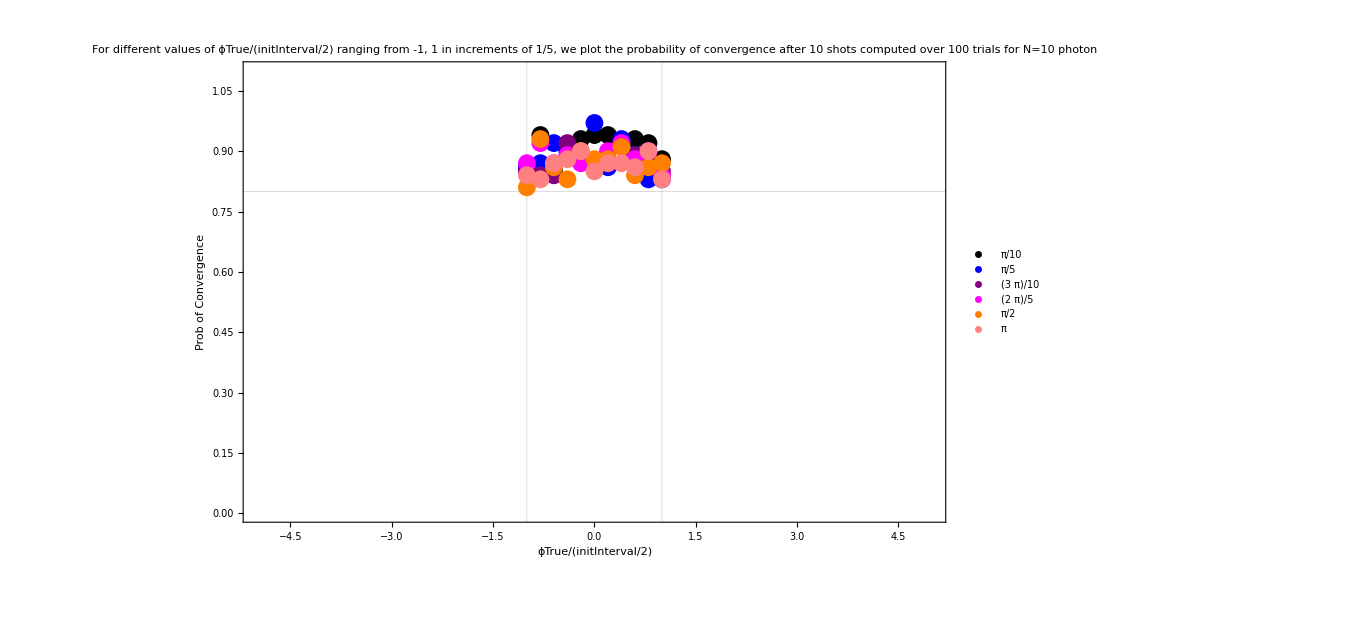

```mathematica
plot101=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=10 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

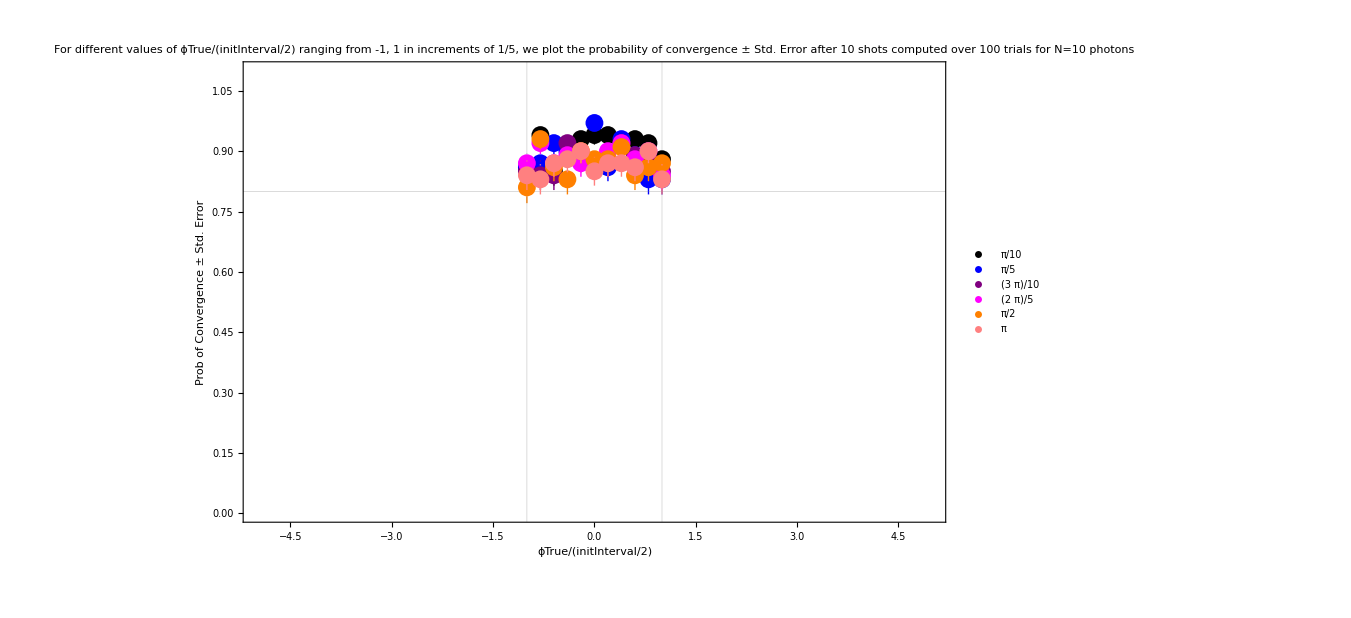

```mathematica
plot102=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=10 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

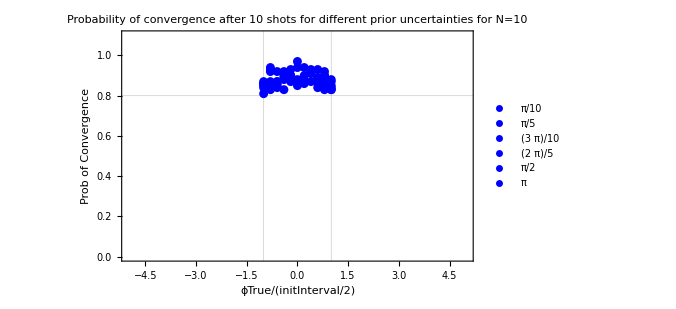

```mathematica
plot103=Show[ListPlot[plot[[1,1]],PlotStyle->{Blue, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=10",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Blue, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Blue,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Blue,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

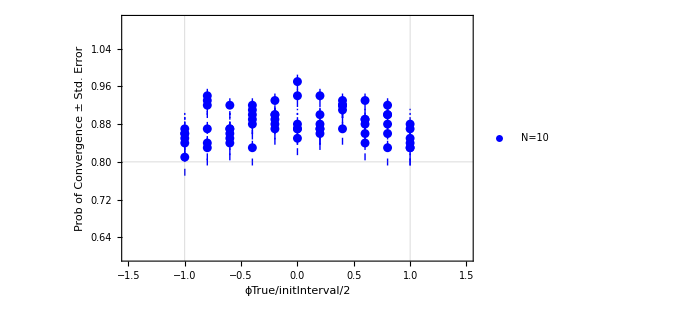

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"N=10"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

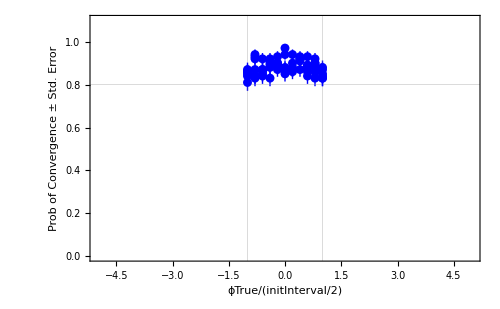
```mathematica
plot104=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
z1
```

((0.86
0.0346987) | (0.94
0.0237487) | (0.85
0.0357071) | (0.91
0.0286182) | (0.93
0.0255147) | (0.94
0.0237487) | (0.94
0.0237487) | (0.92
0.0271293) | (0.93
0.0255147) | (0.92
0.0271293) | (0.88
0.0324962)
(0.86
0.0346987) | (0.87
0.0336303) | (0.92
0.0271293) | (0.9
0.03) | (0.89
0.031289) | (0.97
0.0170587) | (0.86
0.0346987) | (0.93
0.0255147) | (0.89
0.031289) | (0.83
0.0375633) | (0.83
0.0375633)
(0.85
0.0357071) | (0.84
0.0366606) | (0.84
0.0366606) | (0.92
0.0271293) | (0.88
0.0324962) | (0.87
0.0336303) | (0.87
0.0336303) | (0.92
0.0271293) | (0.89
0.031289) | (0.88
0.0324962) | (0.85
0.0357071)
(0.87
0.0336303) | (0.92
0.0271293) | (0.87
0.0336303) | (0.89
0.031289) | (0.87
0.0336303) | (0.87
0.0336303) | (0.9
0.03) | (0.92
0.0271293) | (0.88
0.0324962) | (0.9
0.03) | (0.84
0.0366606)
(0.81
0.0392301) | (0.93
0.0255147) | (0.86
0.0346987) | (0.83
0.0375633) | (0.9
0.03) | (0.88
0.0324962) | (0.88
0.0324962) | (0.91
0.0286182) | (0.84
0.0366606) | (0.86
0.0346987) | (0.87
0.0336303)
(0.84
0.0366606) | (0.83
0.0375633) | (0.87
0.0336303) | (0.88
0.0324962) | (0.9
0.03) | (0.85
0.0357071) | (0.87
0.0336303) | (0.87
0.0336303) | (0.86
0.0346987) | (0.9
0.03) | (0.83
0.0375633))

```mathematica
Average10=Table[MatrixForm[Mean[z1[[1,n]]]],{n,1,Length[Data]}]
```

{(0.910909
0.0280049),(0.886364
0.0309486),(0.873636
0.0329578),(0.884545
0.0317478),(0.87
0.033237),(0.863636
0.0341437)}

```mathematica
Around[Mean[Table[Average10[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average10[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8820.032

```mathematica
Average10=0.8820.032
```

0.8820.032

#### Average Error

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
(*Average y*)
```

```mathematica
Average10y = Table[Mean[y[[1,n]]],{n,1,6}]
```

{0.910909,0.886364,0.873636,0.884545,0.87,0.863636}

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average10σ=Table[ 1/11 √Sum[z1[[1,m,n]]^2,{n,1,11}],{m,1,6}]
```

{0.00853771,0.00948988,0.0099847,0.00961017,0.0100885,0.0103229}

```mathematica
(*(Subscript[y, i] Subscript[σ, i])*)
```

```mathematica
Average10=MatrixForm[Thread[{Average10y,Average10σ}]]
```

(0.910909 | 0.00853771
0.886364 | 0.00948988
0.873636 | 0.0099847
0.884545 | 0.00961017
0.87 | 0.0100885
0.863636 | 0.0103229)

```mathematica
Average10=Table[Around[Average10[[1,n,1]],Average10[[1,n,2]]],{n,1,Length[Data]}]
```

{0.9110.009,0.8860.009,0.8740.010,0.8850.010,0.8700.010,0.8640.010}

```mathematica
(*Total Average*)
```

```mathematica
TotalAverage10y=Mean[Average10[[1,All,1]]]
```

0.881515

```mathematica
TotalAverage10σ = 1/6 √Sum[Average10[[1,n,2]]^2,{n,1,6}]
```

0.00395579

```mathematica
TotalAverage10= Around[TotalAverage10y,TotalAverage10σ]
```

0.8820.004

```mathematica
TotalAverage10=0.880.09
```

0.880.09

### Compare N=3,5,7,10

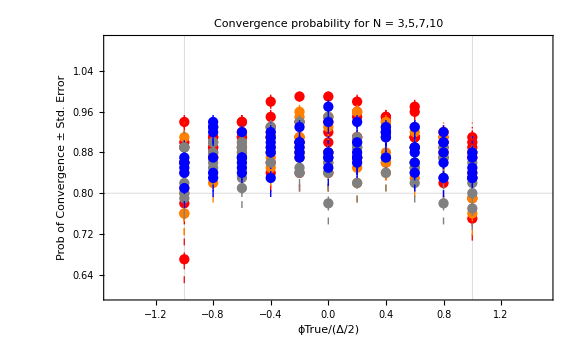

```mathematica
Show[plot34,plot54,plot74,plot104,FrameLabel->{{Style["Prob of Convergence ± Std. Error",Thickness[Large]],None},{HoldForm["\!\(\*FractionBox[\(ϕTrue\), \(Δ/2\)]\)"],None}},PlotLabel->"Convergence probability for N = 3,5,7,10", LabelStyle->{GrayLevel[0]}]
```

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"N=10"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
AverageConvergence={TotalAverage3,TotalAverage5,TotalAverage7,TotalAverage10}
```

{0.9000.004,0.8780.004,0.8680.004,0.8820.004}

```mathematica
AverageConvergence={0.9000.029,0.8780.032,0.8680.033,0.8820.032}
```

{0.9000.029,0.8780.032,0.8680.033,0.8820.032}

```mathematica
AverageConvergence
```

{0.900.09,0.880.09,0.870.10,0.880.09}

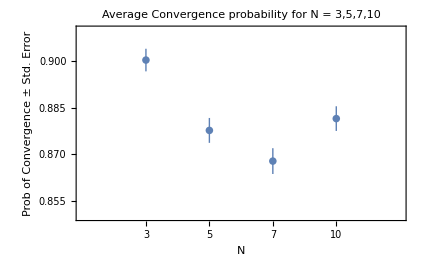

```mathematica
ListPlot[AverageConvergence,PlotRange->{{-0,5},{0.85,0.91}},PlotLabel->"Average Convergence probability for N = 3,5,7,10", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}]
```

```mathematica
AverageConvergence2=MatrixForm[{{Average3[[1]], Average3[[2]]},{Average5[[1]], Average5[[2]]},{Average7[[1]], Average7[[2]]},{Average10[[1]], Average10[[2]]}}]
```

(0.900303 | 0.0286173
0.877727 | 0.0320042
0.867879 | 0.0333102
0.881515 | 0.03184)

```mathematica
Mean[AverageConvergence2[[1]]]
```

{0.881856,0.0314429}

## E. Correction Strategy

### N=3

#### N=3 Correction strategy not implemented

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[IsGaussian==True,Δinit=Δnext(*(Δinit+Δnext)/2*),Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
DataNoCorrection=Data
```

{(-π/2 | -1 | 0.889 | π
-(2 π)/5 | -4/5 | 0.893 | π
-(3 π)/10 | -3/5 | 0.883 | π
-π/5 | -2/5 | 0.876 | π
-π/10 | -1/5 | 0.865 | π
0 | 0 | 0.835 | π
π/10 | 1/5 | 0.896 | π
π/5 | 2/5 | 0.875 | π
(3 π)/10 | 3/5 | 0.902 | π
(2 π)/5 | 4/5 | 0.863 | π
π/2 | 1 | 0.904 | π)}

```mathematica
ntrial=1000;
```

```mathematica
DataNoCorrection=MatrixForm[({{-π/2, -1, 0.889, π}, {-(2 π)/5, -4/5, 0.893, π}, {-(3 π)/10, -3/5, 0.883, π}, {-π/5, -2/5, 0.876, π}, {-π/10, -1/5, 0.865, π}, {0, 0, 0.835, π}, {π/10, 1/5, 0.896, π}, {π/5, 2/5, 0.875, π}, {(3 π)/10, 3/5, 0.902, π}, {(2 π)/5, 4/5, 0.863, π}, {π/2, 1, 0.904, π}})]
```

(-π/2 | -1 | 0.889 | π
-(2 π)/5 | -4/5 | 0.893 | π
-(3 π)/10 | -3/5 | 0.883 | π
-π/5 | -2/5 | 0.876 | π
-π/10 | -1/5 | 0.865 | π
0 | 0 | 0.835 | π
π/10 | 1/5 | 0.896 | π
π/5 | 2/5 | 0.875 | π
(3 π)/10 | 3/5 | 0.902 | π
(2 π)/5 | 4/5 | 0.863 | π
π/2 | 1 | 0.904 | π)

```mathematica
DataNoCorrection=MatrixForm[{DataNoCorrection[[1]]}]
```

((-π/2
-1
0.889
π) | (-(2 π)/5
-4/5
0.893
π) | (-(3 π)/10
-3/5
0.883
π) | (-π/5
-2/5
0.876
π) | (-π/10
-1/5
0.865
π) | (0
0
0.835
π) | (π/10
1/5
0.896
π) | (π/5
2/5
0.875
π) | ((3 π)/10
3/5
0.902
π) | ((2 π)/5
4/5
0.863
π) | (π/2
1
0.904
π))

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataNoCorrection[[del,1,n,3]],√(((DataNoCorrection[[del,1,n,3]])(1-DataNoCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataNoCorrection[[1,1]]]}],{del,1, Length[DataNoCorrection]}]]
```

(0.8890.010 | 0.8930.010 | 0.8830.010 | 0.8760.010 | 0.8650.011 | 0.8350.012 | 0.8960.010 | 0.8750.010 | 0.9020.009 | 0.8630.011 | 0.9040.009)

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
z[[1,1,2,1]]
```

0.893

```mathematica
(*Average y*)
```

```mathematica
Average3yNoCorrection = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.8735

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σNoCorrection= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00309182

```mathematica
TotalAverage3NoCorrection = Around[Average3yNoCorrection,Average3σNoCorrection]
```

0.87350.0031

```mathematica
Average3NoCorrection=TotalAverage3NoCorrection
```

0.87350.0031

#### N = 3 Correction strategy applied if Gaussian

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[IsGaussian==True,numOfShotsInGaussian+=1;Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
numOfShotsInGaussian1=numOfShotsInGaussian;
numOfShotsInGaussian=0;
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
numOfShotsInGaussian1
```

3

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.909, π}, {-(2 π)/5, -4/5, 0.898, π}, {-(3 π)/10, -3/5, 0.882, π}, {-π/5, -2/5, 0.889, π}, {-π/10, -1/5, 0.887, π}, {0, 0, 0.884, π}, {π/10, 1/5, 0.887, π}, {π/5, 2/5, 0.893, π}, {(3 π)/10, 3/5, 0.893, π}, {(2 π)/5, 4/5, 0.897, π}, {π/2, 1, 0.919, π}})
```

{{-π/2,-1,0.909,π},{-(2 π)/5,-4/5,0.898,π},{-(3 π)/10,-3/5,0.882,π},{-π/5,-2/5,0.889,π},{-π/10,-1/5,0.887,π},{0,0,0.884,π},{π/10,1/5,0.887,π},{π/5,2/5,0.893,π},{(3 π)/10,3/5,0.893,π},{(2 π)/5,4/5,0.897,π},{π/2,1,0.919,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.909 | π
-(2 π)/5 | -4/5 | 0.898 | π
-(3 π)/10 | -3/5 | 0.882 | π
-π/5 | -2/5 | 0.889 | π
-π/10 | -1/5 | 0.887 | π
0 | 0 | 0.884 | π
π/10 | 1/5 | 0.887 | π
π/5 | 2/5 | 0.893 | π
(3 π)/10 | 3/5 | 0.893 | π
(2 π)/5 | 4/5 | 0.897 | π
π/2 | 1 | 0.919 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.9090.009 | 0.8980.010 | 0.8820.010 | 0.8890.010 | 0.8870.010 | 0.8840.010 | 0.8870.010 | 0.8930.010 | 0.8930.010 | 0.8970.010 | 0.9190.009)

```mathematica
(*Average y*)
```

```mathematica
Average3yG = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.8915

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σG= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00292892

```mathematica
TotalAverage3G = Around[Average3yG,Average3σG]
```

0.89150.0029

```mathematica
AverageDataCorrectionG=TotalAverage3G
```

0.89150.0029

#### N = 3, Correction applied in the first 5 shots

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[shots<=5,Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.908, π}, {-(2 π)/5, -4/5, 0.894, π}, {-(3 π)/10, -3/5, 0.899, π}, {-π/5, -2/5, 0.898, π}, {-π/10, -1/5, 0.913, π}, {0, 0, 0.914, π}, {π/10, 1/5, 0.887, π}, {π/5, 2/5, 0.914, π}, {(3 π)/10, 3/5, 0.902, π}, {(2 π)/5, 4/5, 0.908, π}, {π/2, 1, 0.896, π}})
```

{{-π/2,-1,0.908,π},{-(2 π)/5,-4/5,0.894,π},{-(3 π)/10,-3/5,0.899,π},{-π/5,-2/5,0.898,π},{-π/10,-1/5,0.913,π},{0,0,0.914,π},{π/10,1/5,0.887,π},{π/5,2/5,0.914,π},{(3 π)/10,3/5,0.902,π},{(2 π)/5,4/5,0.908,π},{π/2,1,0.896,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.908 | π
-(2 π)/5 | -4/5 | 0.894 | π
-(3 π)/10 | -3/5 | 0.899 | π
-π/5 | -2/5 | 0.898 | π
-π/10 | -1/5 | 0.913 | π
0 | 0 | 0.914 | π
π/10 | 1/5 | 0.887 | π
π/5 | 2/5 | 0.914 | π
(3 π)/10 | 3/5 | 0.902 | π
(2 π)/5 | 4/5 | 0.908 | π
π/2 | 1 | 0.896 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.9080.009 | 0.8940.010 | 0.8990.010 | 0.8980.010 | 0.9130.009 | 0.9140.009 | 0.8870.010 | 0.9140.009 | 0.9020.009 | 0.9080.009 | 0.8960.010)

```mathematica
(*Average y*)
```

```mathematica
Average3y5 = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.904333

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σ5= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00282065

```mathematica
TotalAverage35 = Around[Average3y5,Average3σ5]
```

0.90430.0028

```mathematica
AverageDataCorrection5=TotalAverage35
```

0.90430.0028

#### N = 3, Correction applied in the first 10 shots

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[shots<=10,Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.934, π}, {-(2 π)/5, -4/5, 0.943, π}, {-(3 π)/10, -3/5, 0.943, π}, {-π/5, -2/5, 0.951, π}, {-π/10, -1/5, 0.937, π}, {0, 0, 0.943, π}, {π/10, 1/5, 0.938, π}, {π/5, 2/5, 0.943, π}, {(3 π)/10, 3/5, 0.95, π}, {(2 π)/5, 4/5, 0.936, π}, {π/2, 1, 0.955, π}})
```

{{-π/2,-1,0.934,π},{-(2 π)/5,-4/5,0.943,π},{-(3 π)/10,-3/5,0.943,π},{-π/5,-2/5,0.951,π},{-π/10,-1/5,0.937,π},{0,0,0.943,π},{π/10,1/5,0.938,π},{π/5,2/5,0.943,π},{(3 π)/10,3/5,0.95,π},{(2 π)/5,4/5,0.936,π},{π/2,1,0.955,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.934 | π
-(2 π)/5 | -4/5 | 0.943 | π
-(3 π)/10 | -3/5 | 0.943 | π
-π/5 | -2/5 | 0.951 | π
-π/10 | -1/5 | 0.937 | π
0 | 0 | 0.943 | π
π/10 | 1/5 | 0.938 | π
π/5 | 2/5 | 0.943 | π
(3 π)/10 | 3/5 | 0.95 | π
(2 π)/5 | 4/5 | 0.936 | π
π/2 | 1 | 0.955 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.9340.008 | 0.9430.007 | 0.9430.007 | 0.9510.007 | 0.9370.008 | 0.9430.007 | 0.9380.008 | 0.9430.007 | 0.9500.007 | 0.9360.008 | 0.9550.007)

```mathematica
(*Average y*)
```

```mathematica
Average3y10 = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.941833

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σ10= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.0022097

```mathematica
TotalAverage310 = Around[Average3y10,Average3σ10]
```

0.94180.0022

```mathematica
AverageDataCorrection10=TotalAverage310
```

0.94180.0022

#### Comparing different correction strategies for Δini=π

```mathematica
TotalAverage3NoCorrection=0.87350.0031
```

0.87350.0031

```mathematica
(*Gaussian only*)
```

```mathematica
AverageDataCorrectionG=0.89150.0029
```

0.89150.0029

```mathematica
(*5 shots*)
```

```mathematica
AverageDataCorrection5=0.90430.0028
```

0.90430.0028

```mathematica
(*10 shots*)
```

```mathematica
AverageDataCorrection10=0.94180.0022
```

0.94180.0022

### N=10

#### N = 10 Correction strategy not implemented

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[IsGaussian==True,Δinit=Δnext(*(Δinit+Δnext)/2*),Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
Data
```

{(-π/2 | -1 | 0.831 | π
-(2 π)/5 | -4/5 | 0.851 | π
-(3 π)/10 | -3/5 | 0.863 | π
-π/5 | -2/5 | 0.88 | π
-π/10 | -1/5 | 0.864 | π
0 | 0 | 0.865 | π
π/10 | 1/5 | 0.883 | π
π/5 | 2/5 | 0.867 | π
(3 π)/10 | 3/5 | 0.873 | π
(2 π)/5 | 4/5 | 0.862 | π
π/2 | 1 | 0.829 | π)}

```mathematica
Data=({{-π/2, -1, 0.898, π}, {-(2 π)/5, -4/5, 0.922, π}, {-(3 π)/10, -3/5, 0.916, π}, {-π/5, -2/5, 0.915, π}, {-π/10, -1/5, 0.915, π}, {0, 0, 0.901, π}, {π/10, 1/5, 0.92, π}, {π/5, 2/5, 0.913, π}, {(3 π)/10, 3/5, 0.895, π}, {(2 π)/5, 4/5, 0.927, π}, {π/2, 1, 0.922, π}})
```

{{-π/2,-1,0.898,π},{-(2 π)/5,-4/5,0.922,π},{-(3 π)/10,-3/5,0.916,π},{-π/5,-2/5,0.915,π},{-π/10,-1/5,0.915,π},{0,0,0.901,π},{π/10,1/5,0.92,π},{π/5,2/5,0.913,π},{(3 π)/10,3/5,0.895,π},{(2 π)/5,4/5,0.927,π},{π/2,1,0.922,π}}

```mathematica
DataNoCorrection10=MatrixForm[Data[[1]]]
```

(-π/2 | -1 | 0.831 | π
-(2 π)/5 | -4/5 | 0.851 | π
-(3 π)/10 | -3/5 | 0.863 | π
-π/5 | -2/5 | 0.88 | π
-π/10 | -1/5 | 0.864 | π
0 | 0 | 0.865 | π
π/10 | 1/5 | 0.883 | π
π/5 | 2/5 | 0.867 | π
(3 π)/10 | 3/5 | 0.873 | π
(2 π)/5 | 4/5 | 0.862 | π
π/2 | 1 | 0.829 | π)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataNoCorrection10[[del,1,n,3]],√(((DataNoCorrection10[[del,1,n,3]])(1-DataNoCorrection10[[del,1,n,3]]))/ntrial)],{n,1, Length[DataNoCorrection[[1,1]]]}],{del,1, Length[DataNoCorrection]}]]
```

(0.8310.012 | 0.8510.011 | 0.8630.011 | 0.8800.010 | 0.8640.011 | 0.8650.011 | 0.8830.010 | 0.8670.011 | 0.8730.011 | 0.8620.011 | 0.8290.012)

```mathematica
(*Average y*)
```

```mathematica
Average10yNoCorrection = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.859

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average10σNoCorrection= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00329733

```mathematica
TotalAverage10NoCorrection = Around[Average10yNoCorrection,Average10σNoCorrection]
```

0.85900.0033

```mathematica
Average10NoCorrection=TotalAverage10NoCorrection
```

0.85900.0033

#### N = 10 Correction strategy applied if Gaussian

```mathematica
numOfShotsInGaussian=0
```

0

```mathematica
numOfShotsInGaussian
```

0

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[IsGaussian==True,numOfShotsInGaussian+=1;Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
numOfShotsInGaussian1=numOfShotsInGaussian;
numOfShotsInGaussian=0;
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
numOfShotsInGaussian1
```

7

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.903, π}, {-(2 π)/5, -4/5, 0.885, π}, {-(3 π)/10, -3/5, 0.909, π}, {-π/5, -2/5, 0.89, π}, {-π/10, -1/5, 0.883, π}, {0, 0, 0.897, π}, {π/10, 1/5, 0.895, π}, {π/5, 2/5, 0.894, π}, {(3 π)/10, 3/5, 0.876, π}, {(2 π)/5, 4/5, 0.907, π}, {π/2, 1, 0.878, π}})
```

{{-π/2,-1,0.903,π},{-(2 π)/5,-4/5,0.885,π},{-(3 π)/10,-3/5,0.909,π},{-π/5,-2/5,0.89,π},{-π/10,-1/5,0.883,π},{0,0,0.897,π},{π/10,1/5,0.895,π},{π/5,2/5,0.894,π},{(3 π)/10,3/5,0.876,π},{(2 π)/5,4/5,0.907,π},{π/2,1,0.878,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.903 | π
-(2 π)/5 | -4/5 | 0.885 | π
-(3 π)/10 | -3/5 | 0.909 | π
-π/5 | -2/5 | 0.89 | π
-π/10 | -1/5 | 0.883 | π
0 | 0 | 0.897 | π
π/10 | 1/5 | 0.895 | π
π/5 | 2/5 | 0.894 | π
(3 π)/10 | 3/5 | 0.876 | π
(2 π)/5 | 4/5 | 0.907 | π
π/2 | 1 | 0.878 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.9030.009 | 0.8850.010 | 0.9090.009 | 0.8900.010 | 0.8830.010 | 0.8970.010 | 0.8950.010 | 0.8940.010 | 0.8760.010 | 0.9070.009 | 0.8780.010)

```mathematica
(*Average y*)
```

```mathematica
Average10yG = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.8945

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average10σG= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00295212

```mathematica
TotalAverage10G = Around[Average10yG,Average10σG]
```

0.89450.0030

```mathematica
Average10G=TotalAverage10G
```

0.89450.0030

#### N = 10 Correction applied in the first 5 shots

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[shots<=5,Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.857, π}, {-(2 π)/5, -4/5, 0.871, π}, {-(3 π)/10, -3/5, 0.866, π}, {-π/5, -2/5, 0.903, π}, {-π/10, -1/5, 0.89, π}, {0, 0, 0.895, π}, {π/10, 1/5, 0.894, π}, {π/5, 2/5, 0.897, π}, {(3 π)/10, 3/5, 0.888, π}, {(2 π)/5, 4/5, 0.885, π}, {π/2, 1, 0.863, π}})
```

{{-π/2,-1,0.857,π},{-(2 π)/5,-4/5,0.871,π},{-(3 π)/10,-3/5,0.866,π},{-π/5,-2/5,0.903,π},{-π/10,-1/5,0.89,π},{0,0,0.895,π},{π/10,1/5,0.894,π},{π/5,2/5,0.897,π},{(3 π)/10,3/5,0.888,π},{(2 π)/5,4/5,0.885,π},{π/2,1,0.863,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.857 | π
-(2 π)/5 | -4/5 | 0.871 | π
-(3 π)/10 | -3/5 | 0.866 | π
-π/5 | -2/5 | 0.903 | π
-π/10 | -1/5 | 0.89 | π
0 | 0 | 0.895 | π
π/10 | 1/5 | 0.894 | π
π/5 | 2/5 | 0.897 | π
(3 π)/10 | 3/5 | 0.888 | π
(2 π)/5 | 4/5 | 0.885 | π
π/2 | 1 | 0.863 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.8570.011 | 0.8710.011 | 0.8660.011 | 0.9030.009 | 0.8900.010 | 0.8950.010 | 0.8940.010 | 0.8970.010 | 0.8880.010 | 0.8850.010 | 0.8630.011)

```mathematica
(*Average y*)
```

```mathematica
Average10y5 = Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.880333

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average10σ5= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.00306545

```mathematica
TotalAverage105= Around[Average10y5,Average10σ5]
```

0.88030.0031

```mathematica
Average105=TotalAverage105
```

0.88030.0031

#### N = 10 Correction applied in the first 10 shots

```mathematica
Data = Table[
GridOfϕTrue=Table[
ntrial=1000;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue = phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
GetVariance[1,nph,delta];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->(ϕTrue-ϕtilde)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=RandomReal[{0,1}];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
variance=finalVariance/.OptState;
(*with the following average variance*)
variance=Total[variance,2];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];*)
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
(*CORRECTION STRATEGY IMPLEMENTED*)
If[shots<=10,Δinit=(*Δinit=Δnext*)(Δinit+Δnext)/2,Δinit=Δnext];
(*Print[{"IsGaussian ="IsGaussian,Δinit,Δnext}];*)
,{shots,1,nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
{ϕTrue,ϕTrue/(initInterval/2) ,listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{(*1,2,3,4,5,*)10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data=({{-π/2, -1, 0.898, π}, {-(2 π)/5, -4/5, 0.922, π}, {-(3 π)/10, -3/5, 0.916, π}, {-π/5, -2/5, 0.915, π}, {-π/10, -1/5, 0.915, π}, {0, 0, 0.901, π}, {π/10, 1/5, 0.92, π}, {π/5, 2/5, 0.913, π}, {(3 π)/10, 3/5, 0.895, π}, {(2 π)/5, 4/5, 0.927, π}, {π/2, 1, 0.922, π}})
```

{{-π/2,-1,0.898,π},{-(2 π)/5,-4/5,0.922,π},{-(3 π)/10,-3/5,0.916,π},{-π/5,-2/5,0.915,π},{-π/10,-1/5,0.915,π},{0,0,0.901,π},{π/10,1/5,0.92,π},{π/5,2/5,0.913,π},{(3 π)/10,3/5,0.895,π},{(2 π)/5,4/5,0.927,π},{π/2,1,0.922,π}}

```mathematica
DataCorrection={MatrixForm[Data]}
```

{(-π/2 | -1 | 0.898 | π
-(2 π)/5 | -4/5 | 0.922 | π
-(3 π)/10 | -3/5 | 0.916 | π
-π/5 | -2/5 | 0.915 | π
-π/10 | -1/5 | 0.915 | π
0 | 0 | 0.901 | π
π/10 | 1/5 | 0.92 | π
π/5 | 2/5 | 0.913 | π
(3 π)/10 | 3/5 | 0.895 | π
(2 π)/5 | 4/5 | 0.927 | π
π/2 | 1 | 0.922 | π)}

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[DataCorrection[[del,1,n,3]],√(((DataCorrection[[del,1,n,3]])(1-DataCorrection[[del,1,n,3]]))/ntrial)],{n,1, Length[DataCorrection[[1,1]]]}],{del,1, Length[DataCorrection]}]]
```

(0.8980.010 | 0.9220.008 | 0.9160.009 | 0.9150.009 | 0.9150.009 | 0.9010.009 | 0.9200.009 | 0.9130.009 | 0.8950.010 | 0.9270.008 | 0.9220.008)

```mathematica
(*Average y*)
```

```mathematica
Average10y10= Mean[Table[z[[1,1,n,1]],{n,1,6}]]
```

0.911167

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average10σ10= 1/11 √Sum[z[[1,1,n,2]]^2,{n,1,11}]
```

0.0026842

```mathematica
TotalAverage1010 = Around[Average10y10,Average10σ10]
```

0.91120.0027

```mathematica
Average1010=TotalAverage1010
```

0.91120.0027

#### Comparing different correction strategies for Δini=π

```mathematica
Average10NoCorrection=0.85900.0033
```

0.85900.0033

```mathematica
(*Gaussian only*)
```

```mathematica
Average10G=0.89450.0030
```

0.89450.0030

```mathematica
(*5 shots*)
```

```mathematica
Average105=0.88030.0031
```

0.88030.0031

```mathematica
(*10 shots*)
```

```mathematica
Average1010=0.91120.0027
```

0.91120.0027

### Combined results

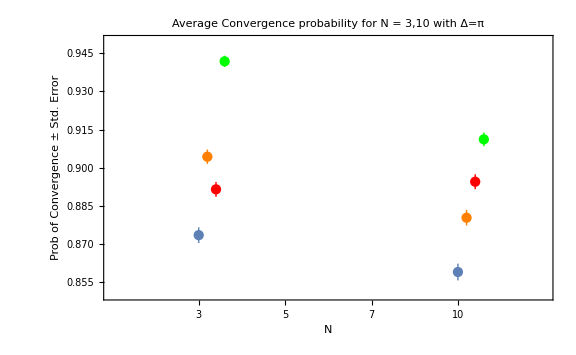

```mathematica
Show[ListPlot[{{1,TotalAverage3NoCorrection},{4,Average10NoCorrection}},PlotLegends->Placed[{"No Correction"},{Center,Center}],PlotRange->{{-0,5},{0.85,0.95}},PlotLabel->"Average Convergence probability for N = 3,10 with Δ=π", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},ImageSize-> Large,FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}],ListPlot[{{1.1,AverageDataCorrection5},{4.1,Average105}},PlotLegends->Placed[{"Correction for 5 shots"},{Center,Center}],PlotStyle->Orange],ListPlot[{{1.2,AverageDataCorrectionG},{4.2,Average10G}},PlotLegends->Placed[{"Correction if Gaussian"},{Center,Center}],PlotStyle->Red],ListPlot[{{1.3,AverageDataCorrection10},{4.3,Average1010}},PlotLegends->Placed[{"Correction for all 10 shots"},{Center,Center}],PlotStyle->Green]]
```

```mathematica
(*check how many steps inside gaussian for N=10*)
```

```mathematica
deltaIn=π
```

π

```mathematica
deltaOut = 1.27 (√deltaIn)/(√10)
```

0.272367

```mathematica
deltaIn=(deltaOut+deltaIn)/2
```

0.366153